## Styles and custom color maps

```mathematica
width=2;
framewidth=1.5;
```

```mathematica
fixLogPlots[gr_]:=gr/.f:(Charting`ScaledTicks|Charting`ScaledFrameTicks)[{Log,Exp}]:>(Part[#,;;, ;;3]&@*f)
OpaqueBox[legend_]:=Graphics[{{White,Opacity[0.5],Rectangle[]},Inset[legend,{0.5,0.6},Center]}]
```

```mathematica
FrameTicksFontSize=20;
FrameFontSize=20;
FrameLabelSize = 12;
PlotOptions={Axes->False,Frame->True,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial",{AbsoluteThickness[framewidth]}],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial",{AbsoluteThickness[framewidth]}]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[framewidth]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[framewidth]]},
LabelStyle->{Directive[Black,FontSize->FrameLabelSize,FontFamily->"Arial"]},
AspectRatio->0.75,ImageSize->400,(*PlotStyle->styles,*)PlotRange->All};
SetOptions[Plot,PlotOptions];
SetOptions[LogPlot,PlotOptions];
SetOptions[LogLogPlot,PlotOptions];
SetOptions[LogLinearPlot,PlotOptions];
SetOptions[ListPlot,PlotOptions];
SetOptions[ListLogPlot,PlotOptions];
SetOptions[ListLogLinearPlot,PlotOptions];
SetOptions[PolarPlot,PlotOptions];
SetOptions[ParametricPlot,PlotOptions];
SetOptions[ListStepPlot,PlotOptions];
PlotOptions3D = {PlotStyle->Directive[Lighter[Lighter[Red]],Specularity[Orange,10],Opacity[1]],PlotPoints->60,MeshStyle->{Opacity[0.5]},Mesh->16,PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->14,FontFamily->"Arial"}};
SetOptions[Plot3D,PlotOptions3D];
ListPlotOptions3D = {PlotStyle->Directive[Lighter[Lighter[Red]],Specularity[Orange,10],Opacity[1]],MeshStyle->{Opacity[0.5]},Mesh->16,PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->14,FontFamily->"Arial"},ColorFunction->"SunsetColors"};
SetOptions[ListPlot3D,ListPlotOptions3D];
DensityPlotOptions = {PlotPoints->60,PlotRange->All,ColorFunction->"SunsetColors",ImageSize->Medium,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[1]]}};
SetOptions[DensityPlot,DensityPlotOptions];
ListDensityPlotOptions = {PlotRange->All,ColorFunction->"SunsetColors",ImageSize->Medium,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[1]]}};
SetOptions[ListDensityPlot,ListDensityPlotOptions];
```

```mathematica
Legending`LegendDump`$DefaultMarkerStyle=EdgeForm[Opacity[1]];
```

```mathematica
ColorHelix[z_] := Module[{start,rot,gamma,amp,angle,red,green,blue,min,max},
start=0.6;
rot=1.5;  
angle=2.0*Pi*(start/3.0+rot*z);
amp = 0.15;
red=z+amp(-0.14861 Cos[angle]+1.78277Sin[angle]);green=z+amp(-0.29227 Cos[angle]-0.90649Sin[angle]);blue=z+amp(1.97294*Cos[angle]);
RGBColor[Abs[Sqrt[1-red]],Abs[Sqrt[1-green]],Abs[Sqrt[1-blue]]]
]
```

## Definitions and Setup

```mathematica
hbarc = 0.197326938; (* GeV fm *)
```

```mathematica
wd =SetDirectory@NotebookDirectory[]
```

/home/sawin/Desktop/CMS_Bottomonia/bottomonia_PbPb5TeV/5 TeV/HNM

## Experimental Data for RAA

#### CMS 5.02 TeV new 2S and 3S data; 1S comes from Phys. Lett. B 790, 270 (2019) [NEW, Jan 23 2023 update]

```mathematica
(* digitized from https://indico.cern.ch/event/895086/contributions/4716202/attachments/2423092/4147702/QM2022_upsilon_soohwanlee_final.pdf *)
```

```mathematica
newDataNpart={({{11.43, 0.790.18}, {31.21, 0.920.15}, {54.42, 0.610.08}, {87.19, 0.520.06}, {131., 0.490.04}, {188.2, 0.400.05}, {262.3, 0.3240.027}, {331.5, 0.3210.029}, {382.3, 0.3190.027}}),({{11.43, 0.600.13}, {31.21, 0.440.08}, {54.42, 0.250.05}, {87.19, 0.1770.030}, {131., 0.1310.024}, {188.2, 0.0960.022}, {262.3, 0.1000.019}, {331.5, 0.0730.021}, {382.3, 0.0780.020}}),({{11.43, 0.530.19}, {42.81, 0.290.07}, {109.1, 0.1090.035}, {269.1, 0.0510.019}})};
```

```mathematica
CMSnpartExpt5020Y1Sdata1 = newDataNpart[[1]];
CMSnpartExpt5020Y2Sdata1 = newDataNpart[[2]];
CMSnpartExpt5020Y3Sdata1 = newDataNpart[[3]];
```

```mathematica
(* QM2022 scanned version was ({{2.0, 0.0466244725738397±0.022027829918767006}, {6.5, 0.0521097046413502±0.023682437310487595}, {12.0, 0.060337552742616±0.018200681308926006}, {22.5, 0.0850210970464135±0.020428839582230504}})*)
```

```mathematica
newDataPT ={({{1., 0.300.13}, {3., 0.360.05}, {5., 0.390.05}, {7.5, 0.400.04}, {10.5, 0.420.06}, {21., 0.430.04}}),({{1.5, 0.0870.019}, {4.5, 0.1220.019}, {7.5, 0.0980.021}, {12., 0.1260.021}, {22.5, 0.1400.022}}),({{2., 0.0650.030}, {6.5, 0.0670.030}, {12., 0.0690.032}, {22.5, 0.1000.026}})}
```

{{{1.,0.300.13},{3.,0.360.05},{5.,0.390.05},{7.5,0.400.04},{10.5,0.420.06},{21.,0.430.04}},{{1.5,0.0870.019},{4.5,0.1220.019},{7.5,0.0980.021},{12.,0.1260.021},{22.5,0.1400.022}},{{2.,0.0650.030},{6.5,0.0670.030},{12.,0.0690.032},{22.5,0.1000.026}}}

```mathematica
CMSnpartExpt5020Y1Sdata1pt=newDataPT[[1]]
CMSnpartExpt5020Y2Sdata1pt=newDataPT[[2]]
CMSnpartExpt5020Y3Sdata1pt=newDataPT[[3]]
```

{{1.,0.300.13},{3.,0.360.05},{5.,0.390.05},{7.5,0.400.04},{10.5,0.420.06},{21.,0.430.04}}

{{1.5,0.0870.019},{4.5,0.1220.019},{7.5,0.0980.021},{12.,0.1260.021},{22.5,0.1400.022}}

{{2.,0.0650.030},{6.5,0.0670.030},{12.,0.0690.032},{22.5,0.1000.026}}

```mathematica
cmsPTint1S=Interpolation[CMSnpartExpt5020Y1Sdata1pt]
cmsPTint2S=Interpolation[CMSnpartExpt5020Y2Sdata1pt]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
ptBins = {2.52.5,8.53.5,21.9.};
ptVals  = {2.5,8.5,21.};
```

```mathematica
pt2S1Srat=(cmsPTint2S/@ptVals)/(cmsPTint1S/@ptVals);
Transpose[{ptBins,pt2S1Srat}]
```

{{2.52.5,0.310.10},{8.53.5,0.220.09},{21.9.,0.390.08}}

```mathematica
(*Clear[mapValue]
mapValue[x_]:=x["Value"]*)
```

```mathematica
(*temp= {{ Around[(0+5)/2,(5-0)/2], Around[0.32,0.1]},{ Around[(5+12)/2,(12-5)/2],Around[0.244,0.083]},{ Around[(12+30)/2,(30-12)/2], Around[0.374,0.081]}};
temp[[All,1]]*)
```

#### ALICE 5.02 TeV data from Phys. Lett. B 790, 89 (2019)

```mathematica
ALICEnpartExpt5020Y1S={{{27.01,0.600000},{0.1,0.04}},{{108.6,0.5},{0.05,0.03}},{{223.5,0.35},{0.03,0.02}},{{355.7,0.34},{0.03,0.02}}};
```

```mathematica
pointMap2[x_] := {x[[1,1]],Around[x[[1,2]],Sqrt[x[[2,1]]]^2+x[[2,2]]^2]}
```

```mathematica
ALICEnpartExpt5020Y1Sdata1 = pointMap2 /@ ALICEnpartExpt5020Y1S
```

{{27.01,0.600.10},{108.6,0.500.05},{223.5,0.3500.030},{355.7,0.3400.030}}

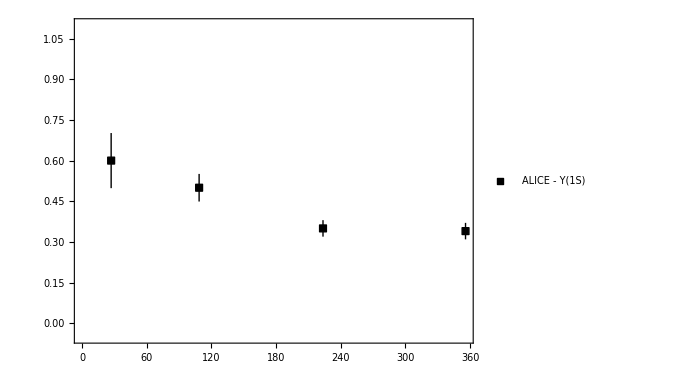

```mathematica
y1sALICEPlot=ListPlot[ALICEnpartExpt5020Y1Sdata1,(*PlotStyle->styles[[1]],*)IntervalMarkersStyle->Black,PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Black}],Black,Rectangle[]},ImageSize->7]},ImageSize->500,PlotRange->{-0.05,1.1},PlotLegends->Placed[LineLegend[{"ALICE - Y(1S)"},LabelStyle->18],{0.8,0.85}]]
```

```mathematica
ALICEptExpt5020Y1S={{{1,0.37},{0.04,0.05}},{{3,0.41},{0.03,0.03}},{{5,0.38},{0.04,0.05}},{{10.5,0.45},{0.04,0.05}}};
```

```mathematica
ALICEptExpt5020Y1Sdata1 = pointMap2 /@ ALICEptExpt5020Y1S
```

{{1,0.370.04},{3,0.4100.031},{5,0.380.04},{10.5,0.450.04}}

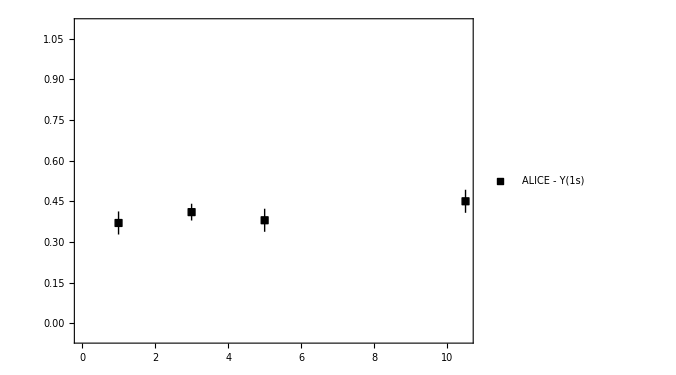

```mathematica
ptALICEPlot=ListPlot[ALICEptExpt5020Y1Sdata1,(*PlotStyle->styles[[1]],*)IntervalMarkersStyle->Black,PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Black}],Black,Rectangle[]},ImageSize->7]},ImageSize->500,PlotRange->{-0.05,1.1},PlotLegends->Placed[LineLegend[{"ALICE - Y(1s)"},LabelStyle->18],{0.75,0.7}]]
```

#### ALICE 5.02 TeV data from 2011.05758

```mathematica
ALICEraaC = {{11.761584 ,0.8641449},
{42.445614 ,0.45022938},
{87, 0.45482674},
{131.4, 0.4100887},
{189.2, 0.4003135},
{241.15063 ,0.31416014},
{282.78186, 0.32513508},
{333.3 ,0.3360841},
{384.3,0.3151856}};
```

```mathematica
ALICEraaSys ={0.94372195,
0.47251055,
0.47870088,
0.42600524,
0.42577913,
0.33962578,
0.33786717,
0.35836527,
0.33110362}-ALICEraaC[[All,2]];
```

```mathematica
ALICEraaStat = 
{1.0344381,
0.5059323,
0.50416505,
0.44351333,
0.42896217,
0.34758332,
0.3505993,
0.36632285,
0.34224275}-ALICEraaC[[All,2]];
```

```mathematica
mapPoint[x_] := Around[x[[1]],x[[2]]]
```

```mathematica
ALICEnpartExpt5020Y1Sdata1=Transpose[{ALICEraaC[[All,1]],mapPoint/@Transpose[{ALICEraaC[[All,2]],Sqrt[ALICEraaSys^2 + ALICEraaStat^2]}]}]
```

{{11.7616,0.860.19},{42.4456,0.450.06},{87,0.450.05},{131.4,0.410.04},{189.2,0.400.04},{241.151,0.310.04},{282.782,0.3250.028},{333.3,0.340.04},{384.3,0.3150.031}}

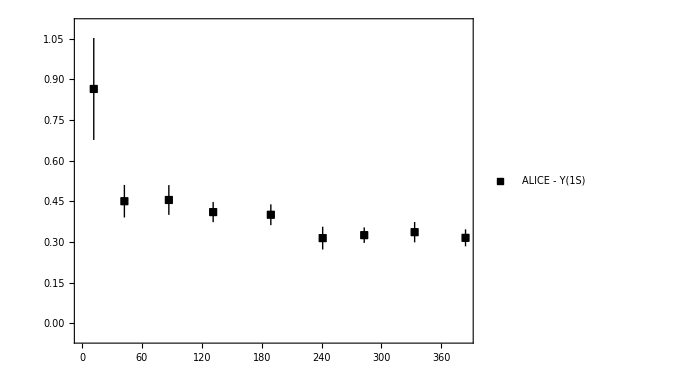

```mathematica
y1sALICEPlot=ListPlot[ALICEnpartExpt5020Y1Sdata1,(*PlotStyle->styles[[1]],*)IntervalMarkersStyle->Black,PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Black}],Black,Rectangle[]},ImageSize->7]},ImageSize->500,PlotRange->{-0.05,1.1},PlotLegends->Placed[LineLegend[{"ALICE - Y(1S)"},LabelStyle->18],{0.8,0.85}]]
```

```mathematica
(* 2s

53.98345 0.2273716
268.98068 0.103969656
54.351997 0.2592004
268.9856 0.12784234
54.35691 0.28307307
268.6236 0.12784378

*)
```

```mathematica
ALICEraaC = {{53.98345, 0.2273716},
{268.98068 ,0.103969656}};
```

```mathematica
ALICEraaSys ={0.2592004,0.12784234}-ALICEraaC[[All,2]];
```

```mathematica
ALICEraaStat = {0.28307307,0.12784378}-ALICEraaC[[All,2]];
```

```mathematica
mapPoint[x_] := Around[x[[1]],x[[2]]]
```

```mathematica
ALICEnpartExpt5020Y2Sdata1=Transpose[{ALICEraaC[[All,1]],mapPoint/@Transpose[{ALICEraaC[[All,2]],Sqrt[ALICEraaSys^2 + ALICEraaStat^2]}]}]
```

{{53.9835,0.230.06},{268.981,0.1040.034}}

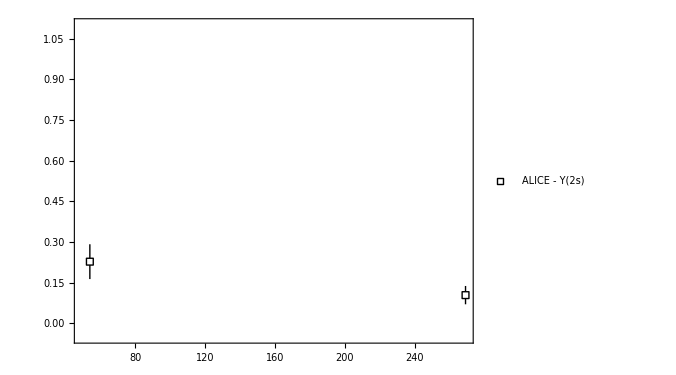

```mathematica
y2sALICEPlot=ListPlot[ALICEnpartExpt5020Y2Sdata1,(*PlotStyle->styles[[1]],*)IntervalMarkersStyle->Black,PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Black}],White,Rectangle[]},ImageSize->7]},ImageSize->500,PlotRange->{-0.05,1.1},PlotLegends->Placed[LineLegend[{"ALICE - Y(2s)"},LabelStyle->18],{0.8,0.85}]]
```

#### ATLAS data (From Wuhan quark matter talk)

```mathematica
({{8.3, 0.790.18}, {30.6, 0.920.15}, {53.9, 0.610.08}, {87., 0.520.06}, {131.4, 0.490.04}, {189.2, 0.400.05}, {264.2, 0.3240.027}, {333.3, 0.3210.029}, {384.3, 0.3190.027}})
```

{{8.3,0.790.18},{30.6,0.920.15},{53.9,0.610.08},{87.,0.520.06},{131.4,0.490.04},{189.2,0.400.05},{264.2,0.3240.027},{333.3,0.3210.029},{384.3,0.3190.027}}

```mathematica
ATLASpts1s = {{22.4492,0.790.16},{70.4292,0.520.12},{131.4,0.430.09},{189.2,0.350.07},{243.168,0.290.06},{285.471,0.270.05},{333.3,0.290.05},{384.3,0.250.05}};
```

```mathematica
ATLASpts2s ={{46.9528,0.350.14},{160.763,0.130.11},{264.2,0.080.05}}
```

{{46.9528,0.350.14},{160.763,0.130.11},{264.2,0.080.05}}

```mathematica
ATLASpts1spt={{1,0.240.13},{3,0.270.07},{5,0.310.06},{7.5,0.370.09},{10.5,0.310.06},{21,0.340.05}}
```

{{1,0.240.13},{3,0.270.07},{5,0.310.06},{7.5,0.370.09},{10.5,0.310.06},{21,0.340.05}}

```mathematica
(*xvals = Import["/Users/mstrick6/Desktop/ATLASy2spt.csv"][[7;;All]][[1;;3]][[All,1]]
pts=Import["/Users/mstrick6/Desktop/ATLASy2spt.csv"][[7;;All]][[1;;3]][[All,2]]
ptsStat = Import["/Users/mstrick6/Desktop/ATLASy2spt.csv"][[7;;All]][[4;;6]][[All,2]]
ptsSys = Import["/Users/mstrick6/Desktop/ATLASy2spt.csv"][[7;;All]][[7;;9]][[All,2]]*)
```

```mathematica
(*ATLASpts2spt= Table[{xvals[[i]],Around[pts[[i]],Sqrt[(ptsStat[[i]]-pts[[i]])^2+(ptsSys[[i]]-pts[[i]])^2]]},{i,1,Length[xvals]}]*)
```

```mathematica
ATLASpts2spt={{2,0.100.09},{6.5,0.130.07},{19.5,0.100.05}}
```

{{2,0.100.09},{6.5,0.130.07},{19.5,0.100.05}}

#### Combined ALICE, ATLAS, and CMS data

```mathematica
ALICEnpartExpt5020Y1Sdata1
```

{{11.7616,0.860.19},{42.4456,0.450.06},{87,0.450.05},{131.4,0.410.04},{189.2,0.400.04},{241.151,0.310.04},{282.782,0.3250.028},{333.3,0.340.04},{384.3,0.3150.031}}

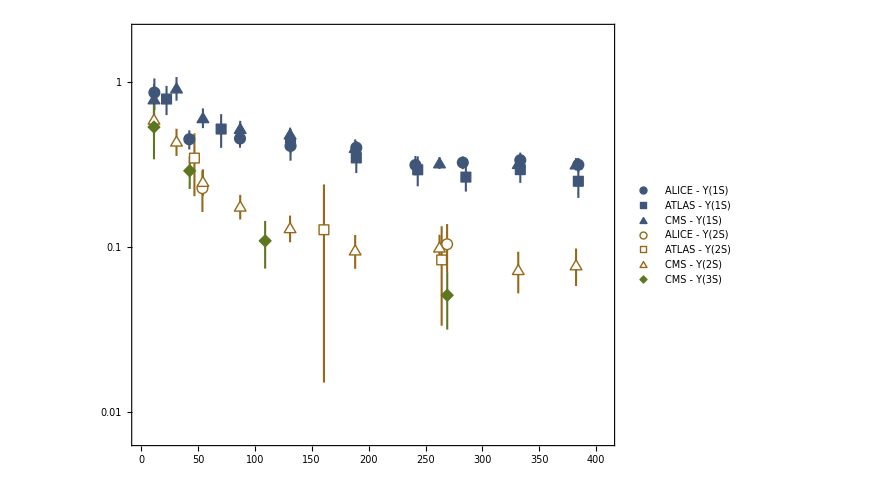

```mathematica
plotColor1= ColorData[97,"ColorList"][[1]]//Darker;
plotColor2= ColorData[97,"ColorList"][[2]]//Darker;
plotColor3= ColorData[97,"ColorList"][[3]]//Darker;
nPartExpPlot =ListLogPlot[{ALICEnpartExpt5020Y1Sdata1,ATLASpts1s,CMSnpartExpt5020Y1Sdata1,ALICEnpartExpt5020Y2Sdata1,ATLASpts2s,CMSnpartExpt5020Y2Sdata1,CMSnpartExpt5020Y3Sdata1},IntervalMarkersStyle->{{AbsoluteThickness[1.5],plotColor1},{AbsoluteThickness[1.5],plotColor1},{AbsoluteThickness[1.5],plotColor1},{AbsoluteThickness[1.5],plotColor2},{AbsoluteThickness[1.5],plotColor2},{AbsoluteThickness[1.5],plotColor2},{AbsoluteThickness[1.5],plotColor3}},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor1}],plotColor1,Disk[]},ImageSize->11],
Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor1}],plotColor1,Rectangle[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor1}],plotColor1,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->12],
Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor2}],White,Disk[]},ImageSize->11],
Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor2}],White,Rectangle[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor2}],White,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->12],Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor3}],plotColor3,Polygon[{{1,0},{0,1},{-1,0},{0,-1}}]},ImageSize->12]},ImageSize->650,PlotLegends->Placed[LineLegend[{"ALICE - Y(1S)","ATLAS - Y(1S)","CMS - Y(1S)","ALICE - Y(2S)","ATLAS - Y(2S)","CMS - Y(2S)","CMS - Y(3S)"},LabelStyle->16,LegendLayout->{"Column",3},LegendMargins->{0,0},LegendMarkerSize->11],{0.63,0.88}],PlotRange->{{0,408},{0.007,2}}]
```

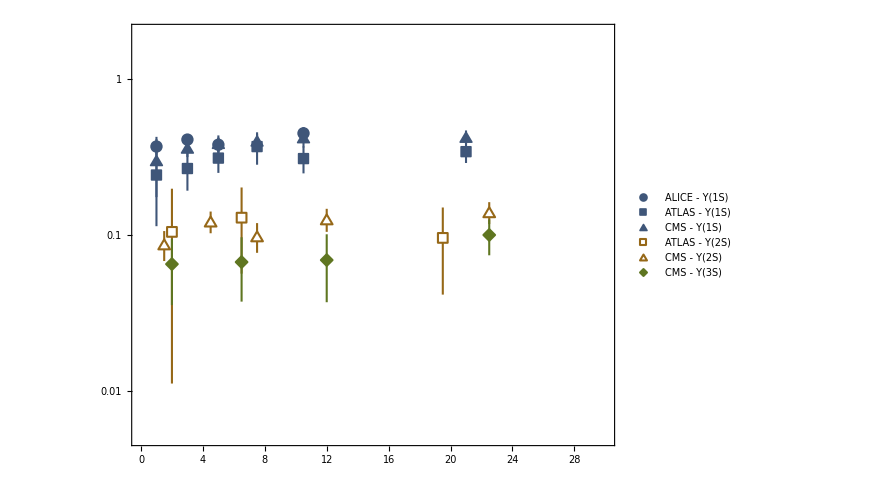

```mathematica
plotColor1= ColorData[97,"ColorList"][[1]]//Darker;
plotColor2= ColorData[97,"ColorList"][[2]]//Darker;
plotColor3= ColorData[97,"ColorList"][[3]]//Darker;
ptExpPlot=ListPlot[{ALICEptExpt5020Y1Sdata1,ATLASpts1spt,CMSnpartExpt5020Y1Sdata1pt,ATLASpts2spt,CMSnpartExpt5020Y2Sdata1pt,CMSnpartExpt5020Y3Sdata1pt},IntervalMarkersStyle->{{AbsoluteThickness[1.5],plotColor1},{AbsoluteThickness[1.5],plotColor1},{AbsoluteThickness[1.5],plotColor1},{AbsoluteThickness[1.5],plotColor2},{AbsoluteThickness[1.5],plotColor2},{AbsoluteThickness[1.5],plotColor3}},ScalingFunctions->{None,"Log"},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1.2],plotColor1}],plotColor1,Disk[]},ImageSize->11],Graphics[{EdgeForm[{AbsoluteThickness[1.2],plotColor1}],plotColor1,Rectangle[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[1.2],plotColor1}],plotColor1,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->12],
Graphics[{EdgeForm[{AbsoluteThickness[1.5],plotColor2}],White,Rectangle[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[1.5],plotColor2}],White,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->12],Graphics[{EdgeForm[{AbsoluteThickness[1.5],plotColor3}],plotColor3,Polygon[{{1,0},{0,1},{-1,0},{0,-1}}]},ImageSize->12
]},ImageSize->650,PlotLegends->Placed[LineLegend[{"ALICE - Y(1S)","ATLAS - Y(1S)","CMS - Y(1S)","ATLAS - Y(2S)","CMS - Y(2S)","CMS - Y(3S)"},LabelStyle->16,LegendLayout->{"Column",3},LegendMargins->{0,0},LegendMarkerSize->11],{0.38,0.89}],PlotRange->{{0,30},{0.005,2}}]
```

#### Rapidity dependence

```mathematica
data1sCMS = {{0.2,0.383±0.03720215047547654},{0.6000000000000001,0.382±0.03538361202590826},{1.,0.394±0.04750789408087881},{1.4,0.362±0.042449970553582246},{1.8,0.378±0.04440720662234903},{2.2,0.415±0.09548298277703729}};
data2sCMS = {{0.4,0.111±0.03162277660168379},{1.2000000000000002,0.13±0.04743416490252569},{2.,0.07±0.05314132102234569}};
data1sALICE = {{2.65,0.433±0.06981403870282825},{2.95,0.396±0.04272001872658766},{3.2,0.398±0.05021951811795888},{3.45,0.338±0.04606517122512409},{3.8,0.305±0.05768882040742383}};

data2sALICE = {{2.9,0.081±0.04459820624195552},{3.65,0.197±0.05315072906367325}};
```

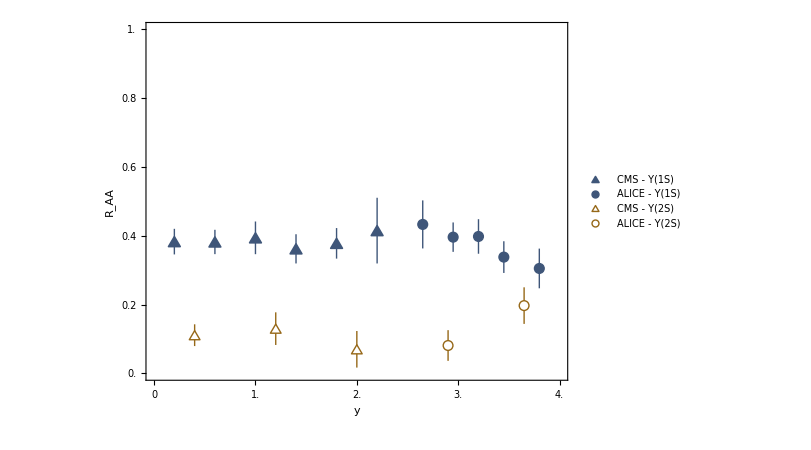

```mathematica
plotColor1= ColorData[97,"ColorList"][[1]]//Darker;
plotColor2= ColorData[97,"ColorList"][[2]]//Darker;
CMS1S=ListPlot[data1sCMS,PlotStyle->plotColor1,IntervalMarkersStyle->plotColor1,PlotMarkers ->Graphics[{EdgeForm[{AbsoluteThickness[1.2],plotColor1}],plotColor1,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->12],PlotRange->{{0,4.0},{0,1}},Frame->True,Axes->False,FrameLabel->{Style["y",17,Black],Style["R_AA",17,Black]},FrameTicks->{{{0.0,0.2,0.4,0.6,0.8,1.0,1.2},None},{{0,0.5,1.0,1.5,2.0,2.5,3.0, 3.5,4.0},None}}, PlotLegends->Placed[LineLegend[{"CMS - Y(1S)"},LabelStyle->18],{0.79,0.90}],ImageSize->500];
ALICE1S=ListPlot[data1sALICE ,PlotStyle->plotColor1,IntervalMarkersStyle->plotColor1,PlotMarkers ->Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor1}],plotColor1,Disk[]},ImageSize->10],PlotRange->{{0,4.0},{0,1}},Frame->True,Axes->False,FrameLabel->{Style["y",17,Black],Style["R_AA",17,Black]},FrameTicks->{{{0.0,0.2,0.4,0.6,0.8,1.0,1.2},None},{{0,0.5,1.0,1.5,2.0,2.5,3.0, 3.5,4.0},None}}, PlotLegends->Placed[LineLegend[{"ALICE - Y(1S)"},LabelStyle->18],{0.8,0.85}],ImageSize->500];
CMS2S=ListPlot[data2sCMS,PlotStyle->plotColor2,IntervalMarkersStyle->plotColor2,PlotMarkers ->Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor2}],White,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->11],PlotRange->{{0,4.0},{0,1}},Frame->True,Axes->False,FrameLabel->{Style["y",17,Black],Style["R_AA",17,Black]},FrameTicks->{{{0.0,0.2,0.4,0.6,0.8,1.0,1.2},None},{{0,0.5,1.0,1.5,2.0,2.5,3.0, 3.5,4.0},None}}, PlotLegends->Placed[LineLegend[{"CMS - Y(2S)"},LabelStyle->18],{0.79,0.80}],ImageSize->500];
ALICE2S=ListPlot[data2sALICE ,PlotStyle->plotColor2,IntervalMarkersStyle->plotColor2,PlotMarkers ->Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor2}],White,Disk[]},ImageSize->10],PlotRange->{{0,4.0},{0,1}},Frame->True,Axes->False,FrameLabel->{Style["y",17,Black],Style["R_AA",17,Black]},FrameTicks->{{{0.0,0.2,0.4,0.6,0.8,1.0,1.2},None},{{0,0.5,1.0,1.5,2.0,2.5,3.0, 3.5,4.0},None}}, PlotLegends->Placed[LineLegend[{"ALICE - Y(2S)"},LabelStyle->18],{0.8,0.75}],ImageSize->500];
expPlotY=Show[{CMS1S,ALICE1S,CMS2S,ALICE2S},ImageSize->600]
```

#### Rapidity dependence (Log Scale)

```mathematica
data1sCMS = {{0.2,0.383±0.03720215047547654},{0.6000000000000001,0.382±0.03538361202590826},{1.,0.394±0.04750789408087881},{1.4,0.362±0.042449970553582246},{1.8,0.378±0.04440720662234903},{2.2,0.415±0.09548298277703729}};
data2sCMS = {{0.4,0.111±0.03162277660168379},{1.2000000000000002,0.13±0.04743416490252569},{2.,0.07±0.05314132102234569}};
data1sALICE = {{2.65,0.433±0.06981403870282825},{2.95,0.396±0.04272001872658766},{3.2,0.398±0.05021951811795888},{3.45,0.338±0.04606517122512409},{3.8,0.305±0.05768882040742383}};

data2sALICE = {{2.9,0.081±0.04459820624195552},{3.65,0.197±0.05315072906367325}};
```

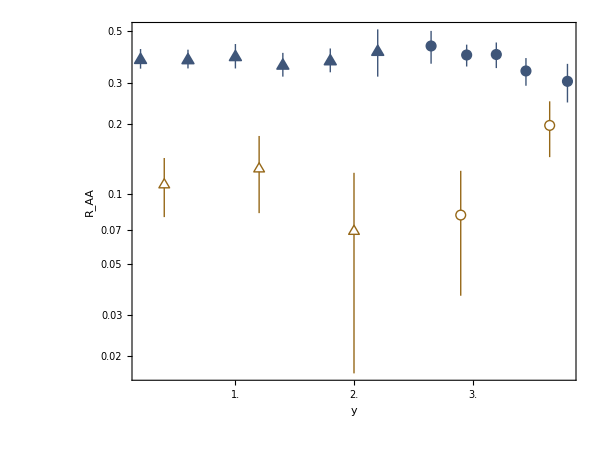

```mathematica
plotColor1= ColorData[97,"ColorList"][[1]]//Darker;
plotColor2= ColorData[97,"ColorList"][[2]]//Darker;
CMS1S=ListLogPlot[data1sCMS,PlotStyle->plotColor1,IntervalMarkersStyle->plotColor1,PlotMarkers ->Graphics[{EdgeForm[{AbsoluteThickness[1.2],plotColor1}],plotColor1,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->12],PlotRange->{{0,4.0},Automatic},Frame->True,Axes->False,FrameLabel->{Style["y",17,Black],Style["R_AA",17,Black]},FrameTicks->{{{0.0,0.2,0.4,0.6,0.8,1.0,1.2},None},{{0,0.5,1.0,1.5,2.0,2.5,3.0, 3.5,4.0},None}}, PlotLegends->Placed[LineLegend[{"CMS - Y(1S)"},LabelStyle->16,LegendMargins->{10,-2}],{Left,Bottom}],ImageSize->500];
ALICE1S=ListLogPlot[data1sALICE ,PlotStyle->plotColor1,IntervalMarkersStyle->plotColor1,PlotMarkers ->Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor1}],plotColor1,Disk[]},ImageSize->10],PlotRange->{{0,4.0},Automatic},Frame->True,Axes->False,FrameLabel->{Style["y",17,Black],Style["R_AA",17,Black]},FrameTicks->{{{0.0,0.2,0.4,0.6,0.8,1.0,1.2},None},{{0,0.5,1.0,1.5,2.0,2.5,3.0, 3.5,4.0},None}}, PlotLegends->Placed[LineLegend[{"ALICE - Y(1S)"},LabelStyle->16,LegendMargins->{10,-2}],{Left,Bottom}],ImageSize->500];
CMS2S=ListLogPlot[data2sCMS,PlotStyle->plotColor2,IntervalMarkersStyle->plotColor2,PlotMarkers ->Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor2}],White,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->11],PlotRange->{{0,4.0},Automatic},Frame->True,Axes->False,FrameLabel->{Style["y",17,Black],Style["R_AA",17,Black]},FrameTicks->{{{0.0,0.2,0.4,0.6,0.8,1.0,1.2},None},{{0,0.5,1.0,1.5,2.0,2.5,3.0, 3.5,4.0},None}}, PlotLegends->Placed[LineLegend[{"CMS - Y(2S)"},LabelStyle->16,LegendMargins->{10,-2}],{Left,Bottom}],ImageSize->500];
ALICE2S=ListLogPlot[data2sALICE ,PlotStyle->plotColor2,IntervalMarkersStyle->plotColor2,PlotMarkers ->Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor2}],White,Disk[]},ImageSize->10],PlotRange->{{0,4.0},Automatic},Frame->True,Axes->False,FrameLabel->{Style["y",17,Black],Style["R_AA",17,Black]},FrameTicks->{{{0.0,0.2,0.4,0.6,0.8,1.0,1.2},None},{{0,0.5,1.0,1.5,2.0,2.5,3.0, 3.5,4.0},None}}, PlotLegends->Placed[LineLegend[{"ALICE - Y(2S)"},LabelStyle->16,LegendMargins->{10,-2}],{Left,Bottom}],ImageSize->500];
expPlotYLog=Show[{CMS1S,ALICE1S,CMS2S,ALICE2S},PlotRange->All,ImageSize->600]
```

## Data files

```mathematica
dataDir = "lhc-3d";
```

```mathematica
labelMap = Association[
{"lhc-3d"->  "κ̂ = 4, γ̂ = 0, T_F = 190 MeV, τ_med = 0.6 fm, with jumps"}
];
```

```mathematica
keys=Keys[labelMap];
figureNameMap=Table[keys[[i]]->keys[[i]],{i,1,Length[keys]}]//Association
```

<|lhc-3d→lhc-3d|>

```mathematica
datafile = "/input/"<>dataDir<>"/datafile-avg.gz";
```

## Read in data

```mathematica
mapData[x_] := {x[[1]],Join[Table[ x[[2]][[i]],{i,1,12,2}],{x[[2,-1]]}],x[[2,-2]]}
```

```mathematica
rawDataAll=mapData/@Partition[Import[wd<>datafile,"Table"],2];
Length[rawDataAll]
```

493536

```mathematica
selectL[lval_]:=Select[rawDataAll,#[[2,7]]==lval&]
```

```mathematica
rawDataS = selectL[0];
Length[rawDataS]
rawDataP = selectL[1];
Length[rawDataP]
```

246768

246768

```mathematica
myR = RandomInteger[{1,Length[rawDataS]}]
rawDataS[[myR ]]
rawDataP[[myR ]]
```

203851

{{6.00746,2.55849,3.08808,-0.266751,27.5005,5.67198,-0.266751},{1.93373,0.0162984,0.,0.0137434,0.,5.04643×10^-12,0},40}

{{6.00746,2.55849,3.08808,-0.266751,27.5005,5.67198,-0.266751},{0.,0.,1.76525×10^-11,0.,4.54278×10^-11,0.,1},40}

```mathematica
sData=Transpose[{rawDataS[[All,2,1]], rawDataS[[All,2,2]], rawDataP[[All,2,3]], rawDataS[[All,2,4]], rawDataP[[All,2,5]], rawDataS[[All,2,6]], rawDataS[[All,3]]}];
mData = rawDataS[[All,1]];
rawData = Transpose[{mData,sData}];
```

```mathematica
bVals=rawData[[All,1,1]]//Union
```

{0,2.32326,4.24791,6.00746,7.77937,9.21228,10.4493,11.5541,12.5619,13.4945,14.3815,15.6555}

## Glauber stuff

```mathematica
(* This was computed externally for a 5.023 TeV PB-PB collision with sigmaNN = 62 *)
nPartVals={406.12232235261763,374.9882778251423,315.8591222901291,243.53796282970384,168.50283662224285,112.39007027735359,70.7871426138262,41.05093670919672,21.292761520545895,9.667790836200798,3.8095328022884103,0.970598659138994};
```

```mathematica
Transpose[{bVals,nPartVals}]
```

{{0,406.122},{2.32326,374.988},{4.24791,315.859},{6.00746,243.538},{7.77937,168.503},{9.21228,112.39},{10.4493,70.7871},{11.5541,41.0509},{12.5619,21.2928},{13.4945,9.66779},{14.3815,3.80953},{15.6555,0.970599}}

```mathematica
nPartVsBInt = Interpolation[Transpose[{bVals,nPartVals}]];
```

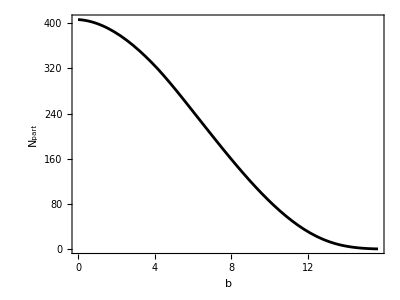

```mathematica
Plot[nPartVsBInt[b],{b,bVals[[1]],bVals[[-1]]},PlotStyle->Black,FrameLabel->{"b","N_part"}]
```

```mathematica
bvscData = Import[wd<>"/input/glauber-data/bvscData.tsv"];
```

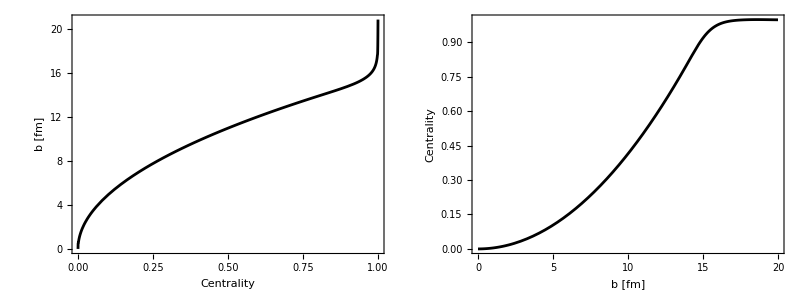

```mathematica
bVsCInt = Interpolation[bvscData];
cVsBInt = Interpolation[Map[Reverse,bvscData]];
Grid[{{Plot[bVsCInt[c],{c,0,1},PlotStyle->Black,FrameLabel->{"Centrality","b [fm]"}],
Plot[cVsBInt[b],{b,0,20},PlotStyle->Black,FrameLabel->{"b [fm]","Centrality"}]}}]
```

```mathematica
cVals=cVsBInt[bVals];
pFunction[c_] = Exp[-c/0.25]/Integrate[Exp[-x/0.25],{x,0,1}]
(*pFunction[c_] = Exp[-c/0.2]/Integrate[Exp[-x/0.2],{x,0,1}]*)
```

4.07463 ⅇ^(-4. c)

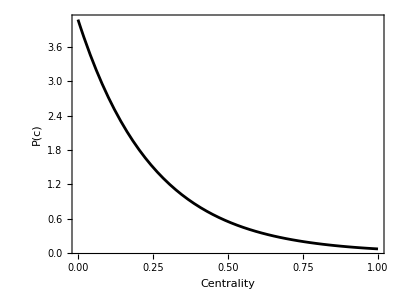

```mathematica
Plot[pFunction[c],{c,0,1},PlotStyle->Black,FrameLabel->{"Centrality","P(c)"}]
```

```mathematica
nbinvsbData = Import[wd<>"/input/glauber-data/nbinvsbData.tsv"];
```

```mathematica
nbinVsb = Interpolation[nbinvsbData]; (* units are fm^2 *)
```

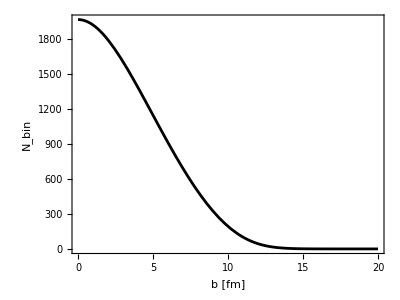

```mathematica
Plot[nbinVsb[b],{b,0,20},PlotStyle->Black,FrameLabel->{"b [fm]","N_bin"}]
```

## Primordial cross sections and branching (feed down) matrix

```mathematica
splitHyperfine[x_] := {x[[1]],x[[2]],x[[3]],x[[3]],x[[3]],x[[4]],x[[5]],x[[5]],x[[5]]}
```

#### From PDG for Upsilon states

```mathematica
(* 1S 2S 1P0 1P1 1P2 3S 2P0 2P1 2P2 *)
```

```mathematica
decayMatrix= {
{1,0,0,0,0,0,0,0,0}, (* 1S *)
{0.2645,1,0,0,0,0,0,0,0}, (* 2S *)
{0.0194,0,1,0,0,0,0,0,0}, (* χb0(1P) *)
{0.352,0,0,1,0,0,0,0,0}, (* χb1(1P) *)
{0.18,0,0,0,1,0,0,0,0}, (* χb2(1P) *)
{0.0657,0.106,0,0,0,1,0,0,0}, (* 3S *)
{0.0038,0.0138,0,0,0,0,1,0,0}, (* χb0(2P) *)
{0.1153,0.181,0,0.0091,0,0,0,1,0}, (* χb1(2P) *)
{0.077,0.089,0,0,0.0051,0,0,0,1}(* χb2(2P) *)
} ;
```

```mathematica
feeddownMatrix = Transpose[decayMatrix];
MatrixForm[feeddownMatrix]
```

(1 | 0.2645 | 0.0194 | 0.352 | 0.18 | 0.0657 | 0.0038 | 0.1153 | 0.077
0 | 1 | 0 | 0 | 0 | 0.106 | 0.0138 | 0.181 | 0.089
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0.0091 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0.0051
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

#### LHC 5 TeV pp

```mathematica
(* 1S 2S 1P0 1P1 1P2 3S 2P0 2P1 2P2 - Extrapolated to 5 TeV *) sigmasEXP = {57.6,19,3.72,13.69,16.1,6.8,3.27,12.0,14.15}
```

{57.6,19,3.72,13.69,16.1,6.8,3.27,12.,14.15}

```mathematica
sigmas = Inverse[feeddownMatrix].sigmasEXP
```

{43.0147,14.8027,3.72,13.5808,16.0278,6.8,3.27,12.,14.15}

#### Compute 1S branching fractions and check sum rule

```mathematica
plucker1s = Table[If[i==j && i==1,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];plucker2s = Table[If[i==j && i==2,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker1p = Table[If[i==j && i≥3 && i ≤5,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker3s = Table[If[i==j && i==6,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
plucker2p = Table[If[i==j && i≥7 && i ≤9,1,0],{i,1,Length[sigmas]},{j,1,Length[sigmas]}];
```

```mathematica
(feeddownMatrix.plucker1s.sigmas)[[1]]/sigmasEXP[[1]]
```

0.746783

```mathematica
(feeddownMatrix.plucker2s.sigmas)[[1]]/sigmasEXP[[1]]
```

0.0679743

```mathematica
(feeddownMatrix.plucker1p.sigmas)[[1]]/sigmasEXP[[1]]
```

0.134334

```mathematica
(feeddownMatrix.plucker3s.sigmas)[[1]]/sigmasEXP[[1]]
```

0.00775625

```mathematica
(feeddownMatrix.plucker2p.sigmas)[[1]]/sigmasEXP[[1]]
```

0.0431524

```mathematica
0.7467833958680554+0.0679743142013889+0.13433367881944444+0.007756249999999999+0.043152361111111114
```

1.

## Results as a function of impact parameter/centrality

```mathematica
myMap[x_] := Around[x[[1]],x[[2]]]
```

```mathematica
selectB[i_]:=Select[rawData,#[[1,1]]==bVals[[i]]&] 
nQtrajs[i_]:=selectB[i][[All,2,7]]//Total
rAAvsB[i_]:=selectB[i][[All,2]][[All,1;;6]] 
getWeights[i_]:=selectB[i][[All,2,7]]/nQtrajs[i]
rAAavgVsB[i_]:=getWeights[i].rAAvsB[i]
rAAsdevVsB[i_] :=StandardDeviation[rAAvsB[i]]/Sqrt[Length[rAAvsB[i]]]
rAAModel[i_] :=myMap/@Transpose[{rAAavgVsB[i],rAAsdevVsB[i] }]
```

```mathematica
(* 1S 2S 1P 3S 2P 1D *) 
spRes=ParallelTable[rAAModel[i],{i,1,Length[bVals]}]
```

{{0.3530.004,0.05600.0021,0.220.05,0.04420.0014,0.1580.028,0.0002156},{0.3680.004,0.05900.0022,0.1420.030,0.04590.0015,0.1610.025,0.0002016},{0.3890.004,0.06390.0023,0.210.04,0.05160.0016,0.1810.028,0.0001946},{0.4310.004,0.07180.0023,0.200.05,0.05820.0017,0.1620.023,0.0001826},{0.4900.005,0.08070.0024,0.1460.033,0.06540.0017,0.1650.023,0.0001806},{0.5590.005,0.11020.0026,0.230.07,0.08800.0020,0.190.04,0.0001475},{0.6430.005,0.16220.0031,0.410.08,0.12590.0023,0.300.04,0.0001225},{0.7220.005,0.28970.0035,0.780.11,0.22110.0028,0.400.04,0.0000934},{0.8130.005,0.5450.004,0.910.10,0.43890.0034,0.580.05,0.000063228},{0.9170.004,0.8520.004,1.090.07,0.7880.004,0.910.05,0.000021710},{0.98680.0023,0.98500.0023,1.0720.015,0.98330.0022,1.0540.014,5.130.1910^-7},{1.,1.,1.,1.,1.,0.}}

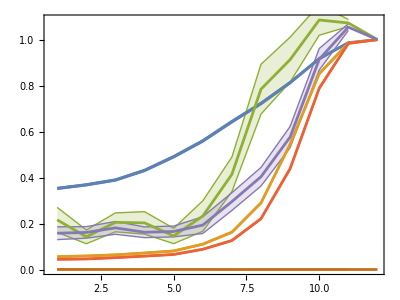

```mathematica
p2=ListPlot[Transpose[spRes],Frame->True,IntervalMarkers->"Bands",PlotRange->All,Joined->True]
```

## Results as a function of impact parameter/centrality (with feed down)

```mathematica
nAAavgVsB[i_]:=0.1 sigmas splitHyperfine[ spRes[[i]] ] nbinVsb[bVals[[i]]]
```

```mathematica
results=ParallelTable[Join[{bVals[[i]]},nAAavgVsB[i]],{i,1,Length[bVals]}]
```

{{0,2979.33.,163.6.,158.40.,576.145.,680.171.,59.01.9,101.18.,372.66.,439.77.},{2.32326,2748.30.,152.6.,92.19.,335.71.,395.83.,54.11.7,91.14.,336.52.,396.62.},{4.24791,2217.24.,125.4.,101.20.,369.74.,435.87.,46.41.4,78.12.,288.44.,339.52.},{6.00746,1684.17.,96.53.0,68.16.,250.60.,295.71.,35.91.0,48.7.,177.25.,208.30.},{7.77937,1121.10.,63.51.9,29.7.,105.24.,124.28.,23.60.6,29.4.,106.15.,124.18.},{9.21228,704.6.,47.71.1,25.7.,92.26.,109.31.,17.50.4,18.53.5,68.13.,80.15.},{10.4493,406.83.2,35.30.7,23.4.,83.15.,98.18.,12.590.23,14.21.9,52.7.,61.8.},{11.5541,203.91.4,28.160.34,19.22.6,70.10.,83.11.,9.870.13,8.70.9,31.83.2,37.4.},{12.5619,89.90.6,20.740.15,8.70.9,31.93.4,38.4.,7.680.06,4.80.4,17.81.4,21.01.7},{13.4945,35.490.17,11.340.05,3.630.22,13.30.8,15.71.0,4.8250.022,2.690.14,9.90.5,11.60.6},{14.3815,12.1720.028,4.1810.010,1.1440.016,4.180.06,4.930.07,1.9170.004,0.9890.014,3.630.05,4.280.06},{15.6555,1.99901,0.687922,0.172878,0.631136,0.744856,0.316014,0.151966,0.557672,0.657588}}

```mathematica
naa1s =results[[All,{1,2}]] ;
naa2s = results[[All,{1,3}]] ;
naa2p0 = results[[All,{1,4}]];
naa2p1 = results[[All,{1,5}]];
naa2p2= results[[All,{1,6}]];
naa3s = results[[All,{1,7}]] ;
naa3p0 = results[[All,{1,8}]];
naa3p1=results[[All,{1,9}]];
naa3p2 = results[[All,{1,10}]];
```

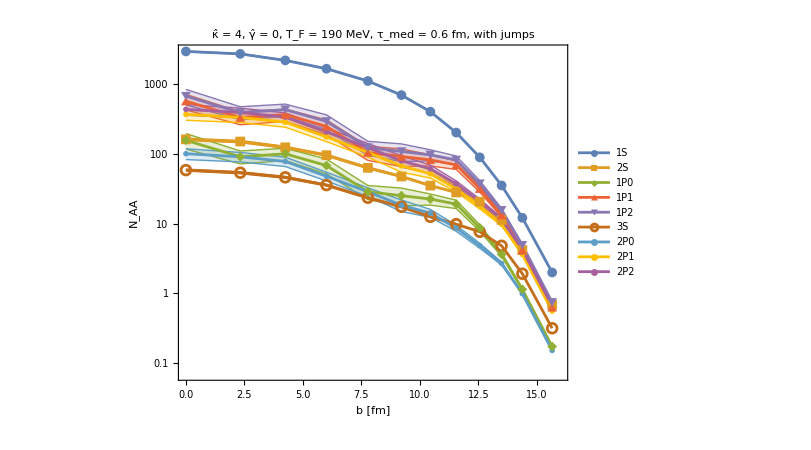

```mathematica
ListLogPlot[{naa1s,naa2s,naa2p0,naa2p1,naa2p2,naa3s,naa3p0,naa3p1,naa3p2},PlotRange->{{0,16},Automatic},Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,PlotMarkers->{Automatic,Medium},IntervalMarkers->"Bands",FrameLabel->{"b [fm]","N_AA"},PlotLegends->Placed[LineLegend[{Style["1S",16],Style["2S",16],Style["1P0",16],Style["1P1",16],Style["1P2",16],Style["3S",16],Style["2P0",16],Style["2P1",16],Style["2P2",16]},LegendMarkerSize->{{60,12}}],Right],PlotLabel->Style[labelMap[dataDir],18]]
```

```mathematica
computeRAAwithFeeddown := Module[{i,j,d,avg},
ParallelTable[
d=feeddownMatrix.Table[nbinVsb[bVals[[i]]]*sigmas[[j]]*0.1,{j,1,9}] ; (* denominator of RAA *)
avg= feeddownMatrix.nAAavgVsB[i];
avg/d
,{i,1,Length[bVals]}]
]
```

```mathematica
nAAavgVsB[1]
```

{2979.33.,163.6.,158.40.,576.145.,680.171.,59.01.9,101.18.,372.66.,439.77.}

```mathematica
myRes=computeRAAwithFeeddown
```

{{0.3030.006,0.0740.004,0.220.05,0.220.05,0.220.05,0.04420.0014,0.1580.028,0.1580.028,0.1580.028},{0.3060.004,0.0770.004,0.1420.030,0.1420.030,0.1420.030,0.04590.0015,0.1610.025,0.1610.025,0.1610.025},{0.3310.005,0.0850.004,0.210.04,0.200.04,0.210.04,0.05160.0016,0.1810.028,0.1810.028,0.1810.028},{0.3610.006,0.0880.004,0.200.05,0.200.05,0.200.05,0.05820.0017,0.1620.023,0.1620.023,0.1620.023},{0.3990.005,0.0960.004,0.1460.033,0.1460.033,0.1460.033,0.06540.0017,0.1650.023,0.1650.023,0.1650.023},{0.4650.007,0.1250.005,0.230.07,0.230.07,0.230.07,0.08800.0020,0.190.04,0.190.04,0.190.04},{0.5610.008,0.1850.006,0.410.08,0.410.07,0.410.07,0.12590.0023,0.300.04,0.300.04,0.300.04},{0.6830.011,0.3080.006,0.780.11,0.780.11,0.780.11,0.22110.0028,0.400.04,0.400.04,0.400.04},{0.7950.010,0.5460.007,0.910.10,0.910.10,0.910.10,0.43890.0034,0.580.05,0.580.05,0.580.05},{0.9340.007,0.8610.007,1.090.07,1.080.07,1.080.07,0.7880.004,0.910.05,0.910.05,0.910.05},{1.00100.0023,0.99760.0026,1.0720.015,1.0720.015,1.0720.015,0.98330.0022,1.0540.014,1.0540.014,1.0540.014},{1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
myRes[[All,1]]
nPartVsBInt[1]
```

{0.3030.006,0.3060.004,0.3310.005,0.3610.006,0.3990.005,0.4650.007,0.5610.008,0.6830.011,0.7950.010,0.9340.007,1.00100.0023,1.}

399.018

```mathematica
raa1sNP = Sort[Transpose[{nPartVsBInt[bVals],myRes[[All,1]]}],#1[[1]]<#2[[1]]&]; 
raa2sNP = Sort[Transpose[{nPartVsBInt[bVals],myRes[[All,2]]}],#1[[1]]<#2[[1]]&];
raa3sNP = Sort[Transpose[{nPartVsBInt[bVals],myRes[[All,6]]}],#1[[1]]<#2[[1]]&];
```

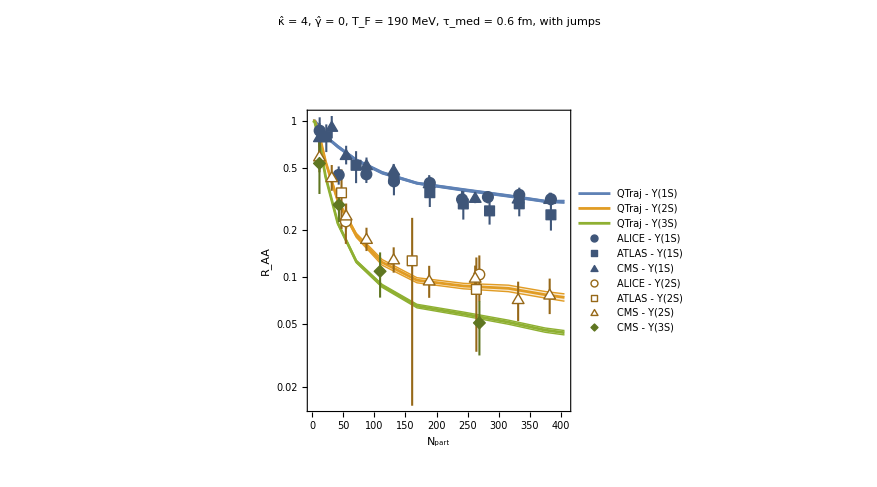

```mathematica
withFDnp=ListLogPlot[{raa1sNP,raa2sNP,raa3sNP},PlotRange->{{0,408},Automatic},Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,IntervalMarkers->"Bands",FrameLabel->{"N_part","R_AA"},
PlotLegends->Placed[LineLegend[{Style["QTraj - Υ(1S)",14],Style["QTraj - Υ(2S)",14],Style["QTraj - Υ(3S)",14]},LegendMarkerSize->{{49,15}},LegendMargins->20],{Left,Bottom}]];
withFDnpExp=Show[withFDnp,nPartExpPlot ,ImageSize->650,Epilog->Inset[Style["5.02 TeV Pb-Pb\nALICE: p_T < 15 GeV and 2.5 < y < 4\nATLAS: p_T < 15 GeV and |y| < 1.5\nCMS: p_T < 30 GeV and |y| < 2.4\nQTraj:  p_T< 30 GeV and y=0",18,TextAlignment->Left],{155,0.95}],PlotRange->{{0,408},Automatic},PlotLabel->Style[labelMap[dataDir],18]]
```

```mathematica
Export[wd<>"/figures/raavsnpart-"<>figureNameMap[dataDir]<>".pdf",withFDnpExp]
```

/home/sawin/Desktop/CMS_Bottomonia/bottomonia_PbPb5TeV/5 TeV/HNM/figures/raavsnpart-lhc-3d.pdf

```mathematica
raavsnpart = {raa1sNP,raa2sNP,raa3sNP};
fileName = wd<>"/figures/raavsnpart-"<>figureNameMap[dataDir]<>".m";
If[FileExistsQ[fileName],DeleteFile[fileName]];
Save[fileName,raavsnpart ]
```

### Fit Quality

```mathematica
raa1sNPint=Interpolation[raa1sNP,InterpolationOrder->1];
raa2sNPint=Interpolation[raa2sNP,InterpolationOrder->1];
raa3sNPint=Interpolation[raa3sNP,InterpolationOrder->1];
```

```mathematica
getValue[x_]:= x["Value"]
```

```mathematica
getFitMeasure[theoryInt_,data_] := Module[{measure},
((getValue/@((theoryInt/@data[[All,1]] -data[[All,2]])/data[[All,2]]))^2 //Total)/Length[data]
]
```

```mathematica
fitMeasureCMSraw={
getFitMeasure[raa1sNPint,CMSnpartExpt5020Y1Sdata1],
getFitMeasure[raa2sNPint,CMSnpartExpt5020Y2Sdata1]
(*,getFitMeasure[raa3sNPint,CMSnpartExpt5020Y3Sdata1]*) (* Not all experiments have 3S data *)
};
fitMeasureCMS={fitMeasureCMSraw,fitMeasureCMSraw//Total};
```

```mathematica
fitMeasureALICEraw={
getFitMeasure[raa1sNPint,ALICEnpartExpt5020Y1Sdata1],
getFitMeasure[raa2sNPint,ALICEnpartExpt5020Y2Sdata1]
};
fitMeasureALICE={fitMeasureALICEraw,fitMeasureALICEraw//Total};
```

```mathematica
fitMeasureATLASraw={
getFitMeasure[raa1sNPint,ATLASpts1s ],
getFitMeasure[raa2sNPint,ATLASpts2s ]
};
fitMeasureATLAS={fitMeasureATLASraw,fitMeasureATLASraw//Total};
```

```mathematica
fitMeasureSeparated = Mean[{fitMeasureCMS[[1]],fitMeasureALICE[[1]],fitMeasureATLAS[[1]]}]
fitMeasure= Mean[{fitMeasureCMS[[2]],fitMeasureALICE[[2]],fitMeasureATLAS[[2]]}]
```

{0.0239526,0.0231494}

0.047102

## Double ratios vs Npart

### 2s/1s

```mathematica
npartPts=raa1sNP[[All,1]];
raa1sVals = raa1sNP[[All,2]];
raa2sVals = raa2sNP[[All,2]];
ratio2s1s=Transpose[{npartPts,raa2sVals/raa1sVals}];
ratio2s1s[[1,2]]=Around[1,10^(-12)];
```

```mathematica
(* CMS data; January 2023 *)
```

```mathematica
CMSexpDataStat = {{11.43,0.750.23},{31.21,0.480.12},{54.42,0.410.09},{87.19,0.340.07},{131.,0.270.06},{188.2,0.240.06},{262.3,0.310.06},{331.5,0.230.07},{382.3,0.240.07}};
CMSexpDataSys= CMSexpDataStat
```

{{11.43,0.750.23},{31.21,0.480.12},{54.42,0.410.09},{87.19,0.340.07},{131.,0.270.06},{188.2,0.240.06},{262.3,0.310.06},{331.5,0.230.07},{382.3,0.240.07}}

```mathematica
(* ATLAS data *)
```

```mathematica
nvs={46.4,160.3,264.2};
rvs={0.615711,0.348195,0.295117};
errsStat= {0.112527,0.127389,0.129511};
errsSys= {0.097665,0.212315,0.065817};

pts1 = Table[Around[rvs[[i]],errsStat[[i]]],{i,1,Length[rvs]}];
pts2 = Table[Around[rvs[[i]],errsSys[[i]]],{i,1,Length[rvs]}];
```

```mathematica
ATLASexpDataStat=Transpose[{nvs,pts1}]
ATLASexpDataSys=Transpose[{nvs,pts2}]
```

{{46.4,0.620.11},{160.3,0.350.13},{264.2,0.300.13}}

{{46.4,0.620.10},{160.3,0.350.21},{264.2,0.300.07}}

```mathematica
expPlot=ListPlot[{ATLASexpDataStat,ATLASexpDataSys,CMSexpDataStat,CMSexpDataSys},IntervalMarkers->"Fences",(*IntervalMarkersStyle->{Black,Darker[Red],Black,Darker[Red]},*)IntervalMarkersStyle->{{Black,AbsoluteThickness[1.2]},{Darker[Red],AbsoluteThickness[1]}},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Black}],Black,Disk[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[1],Black}],Black,Disk[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[1],Black}],Black,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->11],Graphics[{EdgeForm[{AbsoluteThickness[1],Black}],Black,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->11],
Graphics[{EdgeForm[{AbsoluteThickness[1],Black}],White,Rectangle[]},ImageSize->9],Graphics[{EdgeForm[{AbsoluteThickness[1],Black}],White,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->10]},ImageSize->500,PlotLegends->Placed[LineLegend[{"ATLAS",None,"CMS",None},LabelStyle->16],{0.825,0.84}],PlotRange->{{0,408},{0,1.1}}];
```

```mathematica
theoryPlot=ListPlot[ratio2s1s,IntervalMarkers->"Bands",Joined->True,PlotRange->{{0,408},{0,1.05}},InterpolationOrder->1,ImageSize->600,FrameLabel->{"N_part","[Υ(2S)/Υ(1S)]_PbPb/[Υ(2S)/Υ(1S)]_pp"},PlotLabel->Style[labelMap[dataDir],18],PlotLegends->Placed[LineLegend[{"QTraj"},LabelStyle->16],{0.81,0.73}]];
```

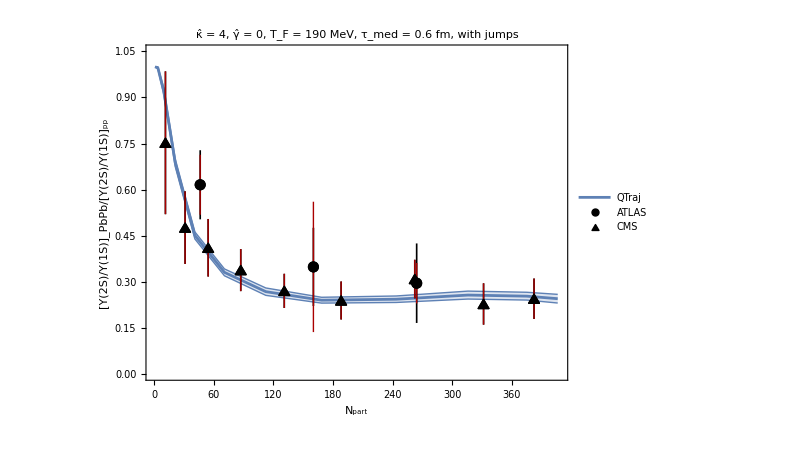

```mathematica
ratioPlot1=Show[theoryPlot,expPlot,PlotLabel->Style[labelMap[dataDir],18]]
```

```mathematica
Export[wd<>"/figures/ratio2s1svsnpart-"<>figureNameMap[dataDir]<>".pdf",ratioPlot1]
```

/home/sawin/Desktop/CMS_Bottomonia/bottomonia_PbPb5TeV/5 TeV/HNM/figures/ratio2s1svsnpart-lhc-3d.pdf

```mathematica
ratio2s1svc = ratio2s1s;
fileName = wd<>"/figures/ratio2s1svsnpart-"<>figureNameMap[dataDir]<>".m";
If[FileExistsQ[fileName],DeleteFile[fileName]];
Save[fileName,ratio2s1svc]
```

```mathematica
ratio2s1sC=Interpolation[Transpose[{Reverse[nPartVals],First /@ ratio2s1s[[All,2]]}],InterpolationOrder->1];
ratio2s1sErr=Last/@ ratio2s1s[[All,2]];
ratio2s1sL=Interpolation[Transpose[{Reverse[nPartVals],First /@ ratio2s1s[[All,2]]-ratio2s1sErr}],InterpolationOrder->1];
ratio2s1sU=Interpolation[Transpose[{Reverse[nPartVals],First /@ ratio2s1s[[All,2]]+ratio2s1sErr}],InterpolationOrder->1];
```

InterpolatingFunction::dmval: Input value {0.00827357} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

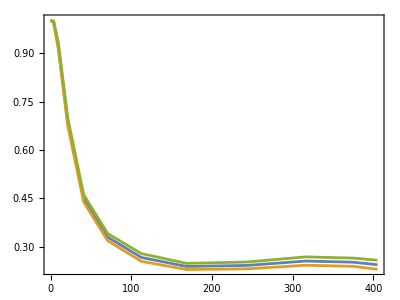

```mathematica
Plot[{ratio2s1sC[npart],ratio2s1sL[npart],ratio2s1sU[npart]},{npart,0,405}]
```

```mathematica
npartVals2S={382.3,331.5,262.3,188.2,131.0,87.19,54.42,31.21,11.43};
```

```mathematica
results2s1s=Table[{npart,ratio2s1sC[npart],ratio2s1sL[npart],ratio2s1sU[npart]},{npart,npartVals2S}];
TableForm[results2s1s,TableHeadings->{None,{"npart","R_AA(Central)","R_AA(Lower)","R_AA(Upper)"}}]
```

npart | R_AA(Central) | R_AA(Lower) | R_AA(Upper)
382.3 | 0.250952 | 0.237914 | 0.26399
331.5 | 0.255494 | 0.242613 | 0.268376
262.3 | 0.24643 | 0.235242 | 0.257617
188.2 | 0.240591 | 0.230807 | 0.250375
131. | 0.258349 | 0.247157 | 0.269542
87.19 | 0.305657 | 0.294148 | 0.317166
54.42 | 0.396573 | 0.385225 | 0.40792
31.21 | 0.56843 | 0.556521 | 0.580339
11.43 | 0.886049 | 0.87542 | 0.896678

```mathematica
headers={"npart","R_AA(Central)","R_AA(Lower)","R_AA(Upper)"};
combinedData2s1s=Prepend[results2s1s,headers];
Export[wd<>"/results2s1s_AA_5TeV.csv",combinedData2s1s]
```

/home/sawin/Desktop/CMS_Bottomonia/bottomonia_PbPb5TeV/5 TeV/HNM/results2s1s_AA_5TeV.csv

```mathematica
results2s1sfull=Table[{npart,ratio2s1sC[npart],ratio2s1sL[npart],ratio2s1sU[npart]},{npart,nPartVals}];
TableForm[results2s1sfull,TableHeadings->{None,{"npart","R_AA(Central)","R_AA(Lower)","R_AA(Upper)"}}]
headers={"npart","R_AA(Central)","R_AA(Lower)","R_AA(Upper)"};
combinedData2s1sfull=Prepend[results2s1sfull,headers];
Export[wd<>"/results2s1s_AA_5TeV_Full.csv",combinedData2s1sfull]
```

npart | R_AA(Central) | R_AA(Lower) | R_AA(Upper)
406.122 | 0.244643 | 0.23052 | 0.258766
374.988 | 0.252888 | 0.240183 | 0.265594
315.859 | 0.256432 | 0.243487 | 0.269376
243.538 | 0.242926 | 0.232354 | 0.253498
168.503 | 0.23976 | 0.230256 | 0.249263
112.39 | 0.267574 | 0.255543 | 0.279605
70.7871 | 0.330446 | 0.319277 | 0.341615
41.0509 | 0.450587 | 0.439094 | 0.462079
21.2928 | 0.687187 | 0.674858 | 0.699515
9.66779 | 0.92158 | 0.911255 | 0.931905
3.80953 | 0.996587 | 0.993128 | 1.00005
0.970599 | 1. | 1. | 1.

/home/sawin/Desktop/CMS_Bottomonia/bottomonia_PbPb5TeV/5 TeV/HNM/results2s1s_AA_5TeV_Full.csv

### 3s/1s

```mathematica
npartPts=raa1sNP[[All,1]];
raa1sVals = raa1sNP[[All,2]];
raa3sVals = raa3sNP[[All,2]];
ratio3s1s=Transpose[{npartPts,raa3sVals/raa1sVals}];
ratio3s1s[[1,2]]= Around[1,10^(-12)]; (* add small error to first point *)
ratio3s1s
```

{{0.970599,1.000000000000010},{3.80953,0.98230.0032},{9.66779,0.8440.008},{21.2928,0.5520.008},{41.0509,0.3230.007},{70.7871,0.2250.005},{112.39,0.1890.005},{168.503,0.1640.005},{243.538,0.1610.005},{315.859,0.1560.005},{374.988,0.1500.005},{406.122,0.1460.006}}

```mathematica
(* CMS data *)
```

```mathematica
CMSexpData ={{11.43,0.70.4},{31.21,0.450.17},{54.42,0.380.18},{87.19,0.280.12},{131.,0.170.11},{188.2,0.100.15},{262.3,0.160.08}}
```

{{11.43,0.70.4},{31.21,0.450.17},{54.42,0.380.18},{87.19,0.280.12},{131.,0.170.11},{188.2,0.100.15},{262.3,0.160.08}}

```mathematica
(* ATLAS DATA *)
nvs = {66.6,180,284,379};
rvs = {0.40936,0.261329,0.197885,0.181269};
errsStat = {0.075528,0.089124,0.084592,0.108761};
errsSys = {0.078549,0.116314,0.043807,0.138973};

pts1 = Table[Around[rvs[[i]],errsStat[[i]]],{i,1,Length[rvs]}];
pts2 = Table[Around[rvs[[i]],errsSys[[i]]],{i,1,Length[rvs]}];

ATLASexpDataStat=Transpose[{nvs,pts1}]
ATLASexpDataSys=Transpose[{nvs,pts2}]
```

{{66.6,0.410.08},{180,0.260.09},{284,0.200.08},{379,0.180.11}}

{{66.6,0.410.08},{180,0.260.12},{284,0.200.04},{379,0.180.14}}

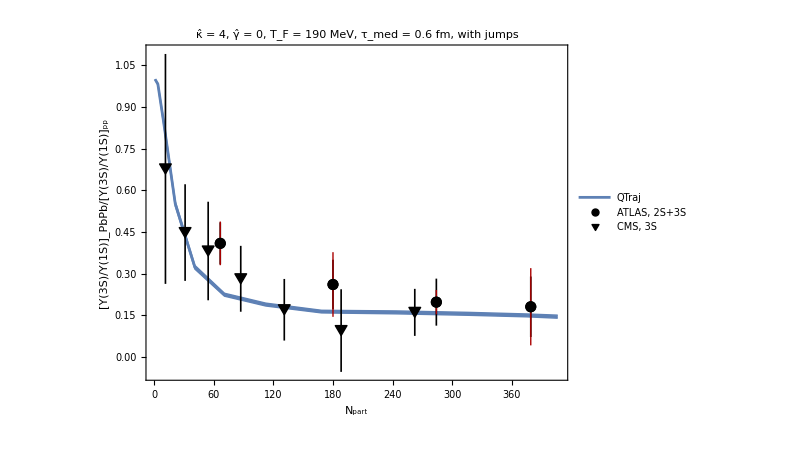

```mathematica
expPlot=ListPlot[{ATLASexpDataStat,ATLASexpDataSys,CMSexpData},IntervalMarkers->"Fences",PlotRange->{{0,408},{0,1.05}},IntervalMarkersStyle->{{Black,AbsoluteThickness[1.2]},{Darker[Red],AbsoluteThickness[1]}},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Black}],Black,Disk[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[1],Black}],Black,Disk[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[1],Black}],Black,Triangle[{{0,0},{1,-1.7},{2,0}}]},ImageSize->12]},PlotLegends->Placed[LineLegend[{"ATLAS, 2S+3S",None,"CMS, 3S"},LabelStyle->16],{0.813,0.85}],ImageSize->550];
theoryPlot=ListPlot[ratio3s1s,IntervalMarkers->"Bands",Joined->True,PlotRange->{{0,408},{-0.06,1.1}},InterpolationOrder->1,ImageSize->600,FrameLabel->{"N_part","[Υ(3S)/Υ(1S)]_PbPb/[Υ(3S)/Υ(1S)]_pp"},PlotLabel->Style[labelMap[dataDir],18],PlotLegends->Placed[LineLegend[{"QTraj"},LabelStyle->16],{0.747,0.74}]];
ratioPlot2=Show[theoryPlot,expPlot,PlotLabel->Style[labelMap[dataDir],18]]
```

```mathematica
Export[wd<>"/figures/ratio3s1svsnpart-"<>figureNameMap[dataDir]<>".pdf",ratioPlot2]
```

/home/sawin/Desktop/CMS_Bottomonia/bottomonia_PbPb5TeV/5 TeV/HNM/figures/ratio3s1svsnpart-lhc-3d.pdf

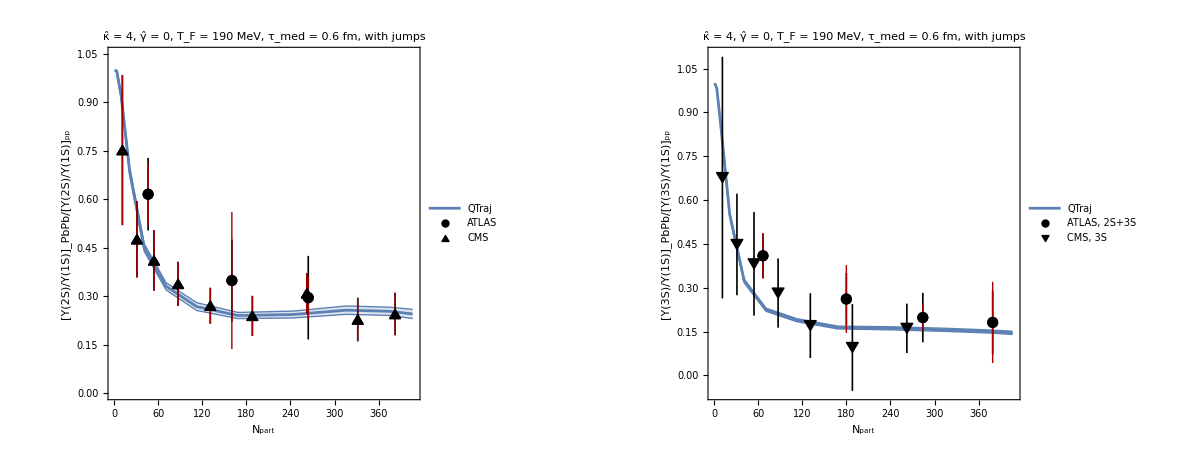

```mathematica
GraphicsGrid[{{ratioPlot1,ratioPlot2}},Spacings->0,ImageSize->1200]
```

```mathematica
ratio3s1svc = ratio3s1s;
fileName = wd<>"/figures/ratio3s1svsnpart-"<>figureNameMap[dataDir]<>".m";
If[FileExistsQ[fileName],DeleteFile[fileName]];
Save[fileName,ratio3s1svc]
```

```mathematica
headers={"npart","R_AA(Central)","R_AA(Lower)","R_AA(Upper)"};
combinedData3s1s=Prepend[ratio3s1s,headers];
Export[wd<>"/results3s1s_AA_5TeV_Full.csv",combinedData3s1s]
```

/home/sawin/Desktop/CMS_Bottomonia/bottomonia_PbPb5TeV/5 TeV/HNM/results3s1s_AA_5TeV_Full.csv

```mathematica
npartVals3S={269.10, 109.10, 42.81, 11.43};
```

```mathematica
ratio3s1sC=Interpolation[Transpose[{Reverse[nPartVals],First /@ ratio3s1s[[All,2]]}],InterpolationOrder->1];
ratio3s1sErr=Last/@ ratio3s1s[[All,2]];
ratio3s1sL=Interpolation[Transpose[{Reverse[nPartVals],First /@ ratio3s1s[[All,2]]-ratio3s1sErr}],InterpolationOrder->1];
ratio3s1sU=Interpolation[Transpose[{Reverse[nPartVals],First /@ ratio3s1s[[All,2]]+ratio3s1sErr}],InterpolationOrder->1];
```

```mathematica
Plot[{ratio3s1sC[npart],ratio3s1sL[npart],ratio3s1sU[npart]},{npart,0,405}];
```

InterpolatingFunction::dmval: Input value {0.00827357} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
results3s1s=Table[{npart,ratio3s1sC[npart],ratio3s1sL[npart],ratio3s1sU[npart]},{npart,npartVals3S}];
TableForm[results3s1s,TableHeadings->{None,{"npart","R_AA(Central)","R_AA(Lower)","R_AA(Upper)"}}]
```

npart | R_AA(Central) | R_AA(Lower) | R_AA(Upper)
269.1 | 0.159198 | 0.153923 | 0.164472
109.1 | 0.191954 | 0.186734 | 0.197173
42.81 | 0.317595 | 0.310954 | 0.324237
11.43 | 0.79988 | 0.792111 | 0.807649

```mathematica
headers={"npart","R_AA(Central)","R_AA(Lower)","R_AA(Upper)"};
combinedData3s1s=Prepend[results3s1s,headers];
Export[wd<>"/results3s1s_AA_5TeV.csv",combinedData3s1s]
```

/home/sawin/Desktop/CMS_Bottomonia/bottomonia_PbPb5TeV/5 TeV/HNM/results3s1s_AA_5TeV.csv

```mathematica
results3s1sfull=Table[{npart,ratio3s1sC[npart],ratio3s1sL[npart],ratio3s1sU[npart]},{npart,nPartVals}];
TableForm[results3s1sfull,TableHeadings->{None,{"npart","R_AA(Central)","R_AA(Lower)","R_AA(Upper)"}}]
headers={"npart","R_AA(Central)","R_AA(Lower)","R_AA(Upper)"};
combinedData3s1sfull=Prepend[results3s1sfull,headers];
Export[wd<>"/results3s1s_AA_5TeV_Full.csv",combinedData3s1sfull]
```

npart | R_AA(Central) | R_AA(Lower) | R_AA(Upper)
406.122 | 0.145567 | 0.140027 | 0.151107
374.988 | 0.150175 | 0.144961 | 0.155389
315.859 | 0.155851 | 0.150553 | 0.161149
243.538 | 0.161028 | 0.155766 | 0.166289
168.503 | 0.163874 | 0.159131 | 0.168616
112.39 | 0.189146 | 0.183935 | 0.194358
70.7871 | 0.224645 | 0.219333 | 0.229956
41.0509 | 0.32344 | 0.316715 | 0.330165
21.2928 | 0.552001 | 0.543675 | 0.560326
9.66779 | 0.844169 | 0.836499 | 0.851838
3.80953 | 0.982285 | 0.979106 | 0.985464
0.970599 | 1. | 1. | 1.

/home/sawin/Desktop/CMS_Bottomonia/bottomonia_PbPb5TeV/5 TeV/HNM/results3s1s_AA_5TeV_Full.csv

### 3s/2s

#### Setup

```mathematica
getWeight[x_] := pFunction[cVsBInt[x[[1,1]]]]
```

```mathematica
mapWithWeight[x_] := Join[ pFunction[cVsBInt[x[[1,1]]]]*splitHyperfine[ x[[2]][[1;;6]] ],{x[[2,7]]}]
```

```mathematica
selectWeights[ptmin_,ptmax_,cmin_,cmax_]:=getWeight/@ Select[rawData,#[[1,5]]≥ptmin&&#[[1,5]]<=ptmax && cVsBInt[#[[1,1]]]≥ cmin &&cVsBInt[#[[1,1]]]≤ cmax&]
```

```mathematica
selectPTweighted[ptmin_,ptmax_,cmin_,cmax_]:=mapWithWeight/@ Select[rawData,#[[1,5]]≥ptmin&&#[[1,5]]<=ptmax&& cVsBInt[#[[1,1]]]≥ cmin &&cVsBInt[#[[1,1]]]≤ cmax&]
```

```mathematica
weightedList[ptmin_,ptmax_,cmin_,cmax_]:=Module[{wtm,res},
wtm = Mean[selectWeights[ptmin,ptmax,cmin,cmax]];
res = selectPTweighted[ptmin,ptmax,cmin,cmax];
MapThread[Append,{res[[All,1;;9]]/wtm,res[[All,-1]]}]
]
```

```mathematica
nAAavgVsPT[ptmin_,ptmax_,cmin_,cmax_]:= Module[{wl,num,qweights},
wl=weightedList[ptmin,ptmax,cmin,cmax];
qweights = wl[[All,-1]];
num = qweights //Total;
Transpose[wl[[All,1;;9]]].qweights/num
]
```

```mathematica
nAAsdevVsPT[ptmin_,ptmax_,cmin_,cmax_]:=Module[{wl},
wl = weightedList[ptmin,ptmax,cmin,cmax];
StandardDeviation[wl]/Sqrt[Length[wl]]
]
nAAVsPT[ptmin_,ptmax_,cmin_,cmax_]:=Module[{avg,err},
avg = nAAavgVsPT[ptmin,ptmax,cmin,cmax];
err= nAAsdevVsPT[ptmin,ptmax,cmin,cmax];
ParallelTable[Around[avg[[i]],err[[i]]]sigmas[[i]],{i,1,9}]
]
```

#### Calc

```mathematica
npartBoundaries={nPartVsBInt[bVsCInt[0]],nPartVsBInt[bVsCInt[0.3]],nPartVsBInt[bVsCInt[0.5]],nPartVsBInt[bVsCInt[0.7]],nPartVsBInt[bVsCInt[0.9]]} //Reverse
```

{2.34582,15.1467,55.4553,139.175,406.122}

```mathematica
raaResAll={feeddownMatrix.nAAVsPT[0,50,0,0.3]/feeddownMatrix.sigmas,
feeddownMatrix.nAAVsPT[0,50,0.3,0.5]/feeddownMatrix.sigmas,
feeddownMatrix.nAAVsPT[0,50,0.5,0.7]/feeddownMatrix.sigmas,
feeddownMatrix.nAAVsPT[0,50,0.7,0.9]/feeddownMatrix.sigmas} //Reverse
```

{{0.9610.005,0.9160.004,1.080.04,1.080.04,1.080.04,0.86650.0024,0.9700.029,0.9700.029,0.9700.029},{0.7280.008,0.4030.005,0.840.08,0.830.08,0.830.08,0.30830.0022,0.4730.030,0.4730.030,0.4730.030},{0.5040.006,0.1490.004,0.310.05,0.310.05,0.310.05,0.10330.0015,0.2340.027,0.2340.027,0.2340.027},{0.32830.0025,0.08150.0018,0.1850.021,0.1850.021,0.1850.021,0.05050.0007,0.1650.012,0.1650.012,0.1650.012}}

```mathematica
(* 2 = 2S; 6 = 3S *)
vals= raaResAll[[All,6]]/ raaResAll[[All,2]];
ratio3s2s= Join[vals,{vals[[-1]]}]
```

{0.9460.005,0.7640.010,0.6930.021,0.6190.016,0.6190.016}

```mathematica
mapValue[x_] := x["Value"]
mapInterval[x_] := x["Interval"]
```

```mathematica
ratio3s2sMin= Transpose[{npartBoundaries,Min/@mapInterval/@ratio3s2s}]; (* Prepare for liststepplot *)
ratio3s2sCenter= Transpose[{npartBoundaries,mapValue/@ratio3s2s}]; (* Prepare for liststepplot *)
ratio3s2sMax= Transpose[{npartBoundaries,Max/@mapInterval/@ratio3s2s}]; (* Prepare for liststepplot *)
```

```mathematica
CMSexpDataStat=({{11.43, 0.900.31}, {42.81, 0.940.21}, {109.1, 0.740.22}, {269.1, 0.570.19}});
CMSexpDataSys=({{11.43, 0.900.15}, {42.81, 0.940.10}, {109.1, 0.740.10}, {269.1, 0.570.10}});
```

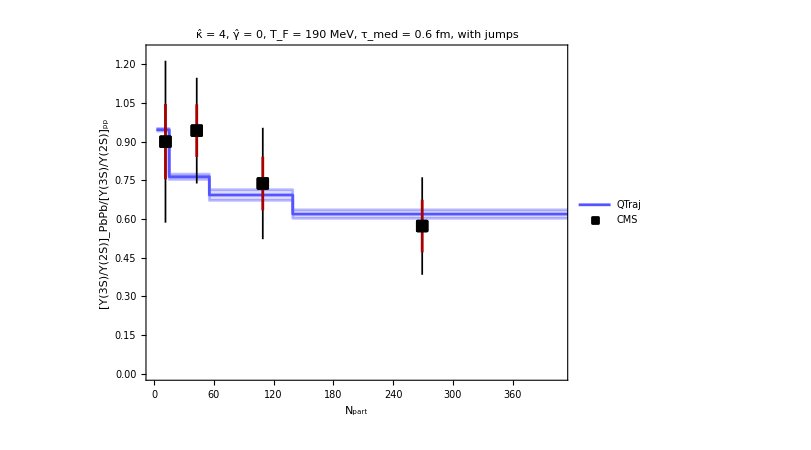

```mathematica
expPlot=ListPlot[{CMSexpDataStat,CMSexpDataSys},IntervalMarkersStyle->{{Black,AbsoluteThickness[1.25]},{Darker[Red],AbsoluteThickness[2]}},IntervalMarkers->"Fences",PlotRange->{{0,408},{0,1.25}},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[2],Black}],Black,Rectangle[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[2],Black}],Black,Rectangle[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[2],Black}],Black,Triangle[{{0,0},{1,-1.7},{2,0}}]},ImageSize->12]},PlotLegends->Placed[LineLegend[{"CMS"},LabelStyle->20],{0.83,0.9}],ImageSize->550];
plotColor =Lighter[Blue];
theoryPlot=ListStepPlot[{ratio3s2sCenter,ratio3s2sMin,ratio3s2sMax},"Right",PlotStyle->{{plotColor,AbsoluteThickness[2]},{plotColor,Opacity[0.4],AbsoluteThickness[2]},{plotColor,Opacity[0.4],AbsoluteThickness[2]}},Joined->True,PlotRange->{{0,407},{0,1.25}},ImageSize->600,FrameLabel->{"N_part","[Υ(3S)/Υ(2S)]_PbPb/[Υ(3S)/Υ(2S)]_pp"},PlotLabel->Style[labelMap[dataDir],18],PlotLegends->Placed[LineLegend[{"QTraj"},LabelStyle->20],{0.83,0.82}], Filling->{2->{3}}];
ratioPlot2=Show[theoryPlot,expPlot,PlotLabel->Style[labelMap[dataDir],18]]
```

```mathematica
Export[wd<>"/figures/ratio3s2svsnpart-"<>figureNameMap[dataDir]<>".pdf",ratioPlot2]
```

/home/sawin/Desktop/CMS_Bottomonia/bottomonia_PbPb5TeV/5 TeV/HNM/figures/ratio3s2svsnpart-lhc-3d.pdf

```mathematica
ratio3s2svc = ratio3s2s;
fileName = wd<>"/figures/ratio3s2svsnpart-"<>figureNameMap[dataDir]<>".m";
If[FileExistsQ[fileName],DeleteFile[fileName]];
Save[fileName,ratio3s2svc]
```

## Results as a function of p_T averaged over centrality (with feed down)

```mathematica
getWeight[x_] := pFunction[cVsBInt[x[[1,1]]]]
```

```mathematica
mapWithWeight[x_] :=Join[  pFunction[cVsBInt[x[[1,1]]]]*splitHyperfine[ x[[2]][[1;;6]] ],{x[[2,7]]}]
```

```mathematica
selectWeights[ptmin_,ptmax_]:=getWeight/@ Select[rawData,#[[1,5]]≥ptmin&&#[[1,5]]<=ptmax&]
```

```mathematica
selectPTweighted[ptmin_,ptmax_]:=mapWithWeight/@ Select[rawData,#[[1,5]]≥ptmin&&#[[1,5]]<=ptmax&]
```

```mathematica
weightedList[ptmin_,ptmax_]:=Module[{wtm,res},
wtm = Mean[selectWeights[ptmin,ptmax]];
res=selectPTweighted[ptmin,ptmax];
MapThread[Append,{res[[All,1;;9]]/wtm,res[[All,-1]]}]
]
```

```mathematica
nAAavgVsPT[ptmin_,ptmax_]:= Module[{wl,num,qweights},
wl=weightedList[ptmin,ptmax];
qweights = wl[[All,-1]];
num = qweights //Total;
Transpose[wl[[All,1;;9]]].qweights/num
]
```

```mathematica
nAAsdevVsPT[ptmin_,ptmax_]:=Module[{wl},
wl = weightedList[ptmin,ptmax];
StandardDeviation[wl]/Sqrt[Length[wl]]
]
nAAVsPT[ptmin_,ptmax_]:=Module[{avg,err},
avg = nAAavgVsPT[ptmin,ptmax];
err= nAAsdevVsPT[ptmin,ptmax];
Table[Around[avg[[i]],err[[i]]]sigmas[[i]],{i,1,9}]
]
```

```mathematica
binwidth=5;
ptmax = 30;
binBoundaries = Range[0,ptmax/binwidth-1]*binwidth
naavsptData=ParallelTable[Join[{x+binwidth/2},feeddownMatrix.nAAVsPT[x,x+binwidth]/feeddownMatrix.sigmas],{x,0,ptmax-binwidth,binwidth}]//N
```

{0,5,10,15,20,25}

{{2.5,2.41.110^-6,0.0000230.000012,1.81.510^-7,1.91.510^-7,1.91.510^-7,8.33.410^-6,2.62.310^-7,2.62.310^-7,2.62.310^-7},{7.5,1.80.810^-6,0.0000169,1.71.210^-8,1.71.110^-8,1.71.210^-8,3.91.510^-6,1.40.910^-8,1.40.910^-8,1.40.910^-8},{12.5,1.81.110^-6,0.0000130.000010,7.5.10^-9,7.5.10^-9,7.5.10^-9,3.31.610^-6,6.4.10^-9,6.4.10^-9,6.4.10^-9},{17.5,9.4.10^-8,9.5.10^-7,1.11.010^-8,1.10.910^-8,1.10.910^-8,6.4.10^-7,9.8.10^-9,9.8.10^-9,9.8.10^-9},{22.5,5.4.10^-7,5.5.10^-6,8.8.10^-9,8.7.10^-9,8.8.10^-9,2.72.410^-6,10.9.10^-9,10.9.10^-9,10.9.10^-9},{27.5,2.41.010^-8,8.4.10^-8,2.01.610^-9,2.01.610^-9,2.01.610^-9,5.22.410^-8,1.81.510^-9,1.81.510^-9,1.81.510^-9}}

```mathematica
mapValue[x_] := x["Value"]
mapInterval[x_] := x["Interval"]
```

```mathematica
data1s=naavsptData[[All,2]];
data2s=naavsptData[[All,3]];
data3s=naavsptData[[All,7]];

naavspt1sDataMin= Transpose[{binBoundaries,Min/@mapInterval/@data1s}];(* Prepare for liststepplot *)
naavspt1sDataCenter= Transpose[{binBoundaries,mapValue/@data1s}]; (* Prepare for liststepplot *)
naavspt1sDataMax= Transpose[{binBoundaries,Max/@mapInterval/@data1s}]; (* Prepare for liststepplot *)

naavspt2sDataMin= Transpose[{binBoundaries,Min/@mapInterval/@data2s}];(* Prepare for liststepplot *)
naavspt2sDataCenter= Transpose[{binBoundaries,mapValue/@data2s}]; (* Prepare for liststepplot *)
naavspt2sDataMax= Transpose[{binBoundaries,Max/@mapInterval/@data2s}]; (* Prepare for liststepplot *)

naavspt3sDataMin= Transpose[{binBoundaries,Min/@mapInterval/@data3s}];(* Prepare for liststepplot *)
naavspt3sDataCenter= Transpose[{binBoundaries,mapValue/@data3s}]; (* Prepare for liststepplot *)
naavspt3sDataMax= Transpose[{binBoundaries,Max/@mapInterval/@data3s}]; (* Prepare for liststepplot *)
```

```mathematica
plotColor1= ColorData[97,"ColorList"][[1]];
plotColor2= ColorData[97,"ColorList"][[2]];
plotColor3= ColorData[97,"ColorList"][[3]];
ptPlot=ListStepPlot[{naavspt1sDataCenter,naavspt1sDataMin,naavspt1sDataMax,naavspt2sDataCenter,naavspt2sDataMin,naavspt2sDataMax,naavspt3sDataCenter,naavspt3sDataMin,naavspt3sDataMax},"Right",ScalingFunctions->{None,"Log"},PlotRange->{Automatic,{0.03,1}},PlotStyle->{
{plotColor1,AbsoluteThickness[2]},{plotColor1,Opacity[0.4],AbsoluteThickness[2]},{plotColor1,Opacity[0.4],AbsoluteThickness[2]},
{plotColor2,AbsoluteThickness[2]},{plotColor2,Opacity[0.4],AbsoluteThickness[2]},{plotColor2,Opacity[0.4],AbsoluteThickness[2]},
{plotColor3,AbsoluteThickness[2]},{plotColor3,Opacity[0.4],AbsoluteThickness[2]},{plotColor3,Opacity[0.4],AbsoluteThickness[2]}
},Joined->True,Filling->{2->{3},5->{6},8->{9}},FrameLabel->{"p_T","R_AA"},PlotLegends->Placed[LineLegend[{Style["QTraj - Υ(1S)",16],None,None,Style["QTraj - Υ(2S)",16],None,None,Style["QTraj - Υ(3S)",16]},LegendMarkerSize->{{47,15}},LegendMargins->10],{Right,Bottom}],ImageSize->650];
```

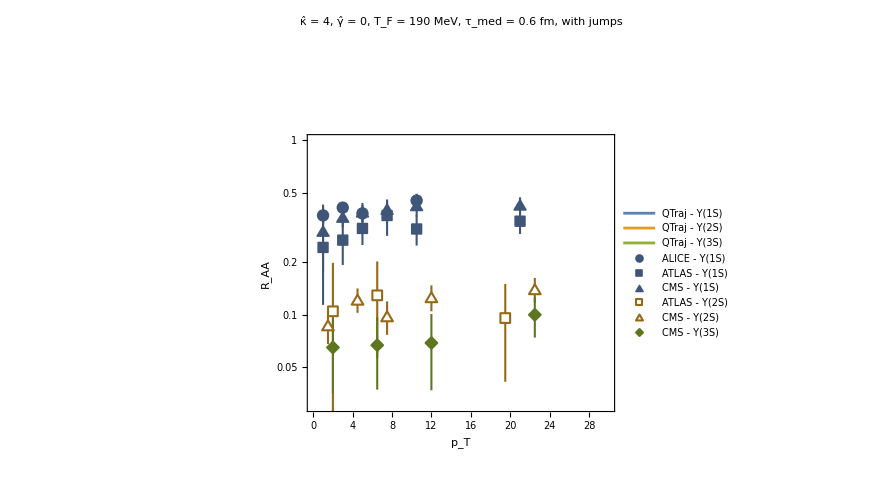

```mathematica
ptPlotwithExp=Show[ptPlot,ptExpPlot,(*PlotRange->{{0,30},{0,1.1}},*)Epilog->Inset[Style["5.02 TeV Pb-Pb\nCMS: 0-100% and |y| < 2.4\nALICE: 0-90% and 2.5 < y < 4\nATLAS:  0-80% and |y| < 1.5\nQTraj:  0-100% and y=0",16,TextAlignment->Left],{6.9,0.95}],PlotLabel->Style[labelMap[dataDir],18]]
```

```mathematica
Export[wd<>"/figures/raavspt-"<>figureNameMap[dataDir]<>".pdf",ptPlotwithExp]
```

/home/sawin/Desktop/CMS_Bottomonia/bottomonia_PbPb5TeV/5 TeV/HNM/figures/raavspt-lhc-octet.pdf

```mathematica
raavspt={data1s,data2s,data3s};
fileName = wd<>"/figures/raavspt-"<>figureNameMap[dataDir]<>".m";
If[FileExistsQ[fileName],DeleteFile[fileName]];
Save[fileName,raavspt]
```

## Results as a function of p_T averaged in specified centrality bins (with feed down)

#### Setup

```mathematica
getWeight[x_] := pFunction[cVsBInt[x[[1,1]]]]
```

```mathematica
mapWithWeight[x_] := Join[ pFunction[cVsBInt[x[[1,1]]]]*splitHyperfine[ x[[2]][[1;;6]] ],{x[[2,7]]}]
```

```mathematica
selectWeights[ptmin_,ptmax_,cmin_,cmax_]:=getWeight/@ Select[rawData,#[[1,5]]≥ptmin&&#[[1,5]]<=ptmax && cVsBInt[#[[1,1]]]≥ cmin &&cVsBInt[#[[1,1]]]≤ cmax&]
```

```mathematica
selectPTweighted[ptmin_,ptmax_,cmin_,cmax_]:=mapWithWeight/@ Select[rawData,#[[1,5]]≥ptmin&&#[[1,5]]<=ptmax&& cVsBInt[#[[1,1]]]≥ cmin &&cVsBInt[#[[1,1]]]≤ cmax&]
```

```mathematica
weightedList[ptmin_,ptmax_,cmin_,cmax_]:=Module[{wtm,res},
wtm = Mean[selectWeights[ptmin,ptmax,cmin,cmax]];
res = selectPTweighted[ptmin,ptmax,cmin,cmax];
MapThread[Append,{res[[All,1;;9]]/wtm,res[[All,-1]]}]
]
```

```mathematica
nAAavgVsPT[ptmin_,ptmax_,cmin_,cmax_]:= Module[{wl,num,qweights},
wl=weightedList[ptmin,ptmax,cmin,cmax];
qweights = wl[[All,-1]];
num = qweights //Total;
Transpose[wl[[All,1;;9]]].qweights/num
]
```

```mathematica
nAAsdevVsPT[ptmin_,ptmax_,cmin_,cmax_]:=Module[{wl},
wl = weightedList[ptmin,ptmax,cmin,cmax];
StandardDeviation[wl]/Sqrt[Length[wl]]
]
nAAVsPT[ptmin_,ptmax_,cmin_,cmax_]:=Module[{avg,err},
avg = nAAavgVsPT[ptmin,ptmax,cmin,cmax];
err= nAAsdevVsPT[ptmin,ptmax,cmin,cmax];
ParallelTable[Around[avg[[i]],err[[i]]]sigmas[[i]],{i,1,9}]
]
```

#### Double ratio plot vs pt (2S/1S)

```mathematica
raaRes1=feeddownMatrix.nAAVsPT[0,5,0,1]/feeddownMatrix.sigmas
```

{2.41.110^-6,0.0000230.000012,1.81.510^-7,1.91.510^-7,1.91.510^-7,8.33.410^-6,2.62.310^-7,2.62.310^-7,2.62.310^-7}

```mathematica
raaRes1[[2,1]]/raaRes1[[1,1]]
raaRes1[[2]]/raaRes1[[1]]
```

9.29724

9.7.

```mathematica
raaRes2=feeddownMatrix.nAAVsPT[5,12,0,1]/feeddownMatrix.sigmas
```

{2.20.810^-6,0.0000198,1.50.910^-8,1.50.910^-8,1.50.910^-8,4.21.410^-6,1.20.710^-8,1.20.710^-8,1.20.710^-8}

```mathematica
raaRes2[[2,1]]/raaRes2[[1,1]]
raaRes2[[2]]/raaRes2[[1]]
```

8.60629

9.5.

```mathematica
raaRes3=feeddownMatrix.nAAVsPT[12,30,0,1]/feeddownMatrix.sigmas
```

{2.21.010^-7,2.21.110^-6,8.4.10^-9,8.4.10^-9,8.4.10^-9,1.40.610^-6,8.4.10^-9,8.4.10^-9,8.4.10^-9}

```mathematica
raaRes3[[2,1]]/raaRes3[[1,1]]
raaRes3[[2]]/raaRes3[[1]]
```

10.0696

10.7.

```mathematica
qtrajResC = {{ Around[(0+5)/2,(5-0)/2], raaRes1[[2]]/raaRes1[[1]]},{ Around[(5+12)/2,(12-5)/2],raaRes2[[2]]/raaRes2[[1]]},{ Around[(12+30)/2,(30-12)/2], raaRes3[[2]]/raaRes3[[1]]}}
```

{{2.52.5,9.7.},{8.53.5,9.5.},{21.9.,10.7.}}

```mathematica
mapValue[x_] := x["Value"]
mapInterval[x_] := x["Interval"]
```

```mathematica
Min/@mapInterval/@qtrajResC [[All,2]]
```

{2.69381,3.60595,3.22357}

```mathematica
qtrajResC2 = Join[qtrajResC,{qtrajResC[[-1]]}]
```

{{2.52.5,9.7.},{8.53.5,9.5.},{21.9.,10.7.},{21.9.,10.7.}}

```mathematica
binsBoundaries= {0,5,12,30};
```

```mathematica
qtrajResMin= Transpose[{binsBoundaries,Min/@mapInterval/@qtrajResC2[[All,2]]}]; (* Prepare for liststepplot *)
qtrajResCenter= Transpose[{binsBoundaries,mapValue/@qtrajResC2[[All,2]]}]; (* Prepare for liststepplot *)
qtrajResMax= Transpose[{binsBoundaries,Max/@mapInterval/@qtrajResC2[[All,2]]}]; (* Prepare for liststepplot *)
```

```mathematica
CMSdata1= {{ Around[(0+5)/2,(5-0)/2], Around[0.32,0.1]},{ Around[(5+12)/2,(12-5)/2],Around[0.244,0.083]},{ Around[(12+30)/2,(30-12)/2], Around[0.374,0.081]}}
CMSdata2= {{ Around[(0+5)/2,(5-0)/2], Around[0.32,0.12]},{ Around[(5+12)/2,(12-5)/2],Around[0.244,0.032]},{ Around[(12+30)/2,(30-12)/2], Around[0.374,0.012]}}
```

{{2.52.5,0.320.10},{8.53.5,0.240.08},{21.9.,0.370.08}}

{{2.52.5,0.320.12},{8.53.5,0.2440.032},{21.9.,0.3740.012}}

```mathematica
CMSdataNew = ({{2.52.5, 0.310.10}, {8.53.5, 0.220.09}, {21.9., 0.390.08}})
```

{{2.52.5,0.310.10},{8.53.5,0.220.09},{21.9.,0.390.08}}

```mathematica
ATLASdata1= {{ Around[(0+4)/2,(4-0)/2], Around[0.375,0.22]},{ Around[(4+9)/2,(9-4)/2],Around[0.387,0.15]},
{ Around[(9+30)/2,(30-9)/2], Around[0.296,0.11]}}
ATLASdata2= {{ Around[(0+4)/2,(4-0)/2], Around[0.375,0.06]},{ Around[(4+9)/2,(9-4)/2],Around[0.387,0.15]},{ Around[(9+30)/2,(30-9)/2], Around[0.296,0.05]}}
```

{{2.02.0,0.380.22},{6.52.5,0.390.15},{20.11.,0.300.11}}

{{2.02.0,0.380.06},{6.52.5,0.390.15},{20.11.,0.300.05}}

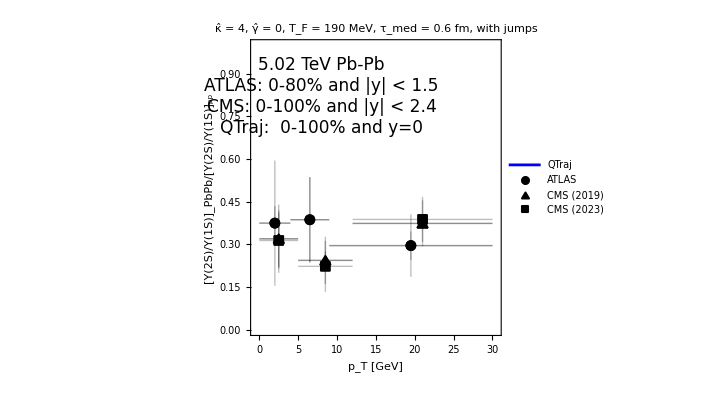

```mathematica
expPlot=ListPlot[{ATLASdata1,ATLASdata2,CMSdata1,CMSdata2,CMSdataNew},PlotRange->{{-0.5,30.5},{0,1}},IntervalMarkers->"Fences",IntervalMarkersStyle->{{AbsoluteThickness[1],Black,Opacity[0.25]}},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1.5],Black}],Black,Disk[]},ImageSize->9],Graphics[{EdgeForm[{AbsoluteThickness[1.5],Black}],Black,Disk[]},ImageSize->9],Graphics[{EdgeForm[{AbsoluteThickness[1.5],Black}],Black,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[1.5],Black}],Black,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->10],
Graphics[{EdgeForm[{AbsoluteThickness[1.5],Black}],Black,Rectangle[]},ImageSize->9],Graphics[{EdgeForm[{AbsoluteThickness[1.5],Black}],White,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->10]},ImageSize->500,PlotLegends->Placed[LineLegend[{"ATLAS",None,"CMS (2019)",None,"CMS (2023)"},LabelStyle->16],{0.83,0.85}]];

plotColor=Blue;theoryPlot=ListStepPlot[{qtrajResCenter,qtrajResMin,qtrajResMax} ,PlotRange->{{-0.5,30.5},{0,1.0}},PlotStyle->{{plotColor,AbsoluteThickness[2]},{plotColor,Opacity[0.3],AbsoluteThickness[2]},{plotColor,Opacity[0.3],AbsoluteThickness[2]}},FrameLabel->{"p_T [GeV]","[Υ(2S)/Υ(1S)]_PbPb/[Υ(2S)/Υ(1S)]_pp"},PlotLegends->Placed[LineLegend[{Style["QTraj",17]},LegendMarkerSize->{20,11}],{0.785,0.685}],Epilog->Inset[Style["5.02 TeV Pb-Pb\nATLAS: 0-80% and |y| < 1.5\nCMS: 0-100% and |y| < 2.4\nQTraj:  0-100% and y=0",17,TextAlignment->Left],{8,0.82}],ImageSize->530, Filling->{2->{3}}];

doubleRatioPTPlot=Show[theoryPlot,expPlot,ImageSize->530,PlotLabel->Style[labelMap[dataDir],18]]
```

```mathematica
Export[wd<>"/figures/ratio-2s1s-vspt-"<>figureNameMap[dataDir]<>".pdf",doubleRatioPTPlot]
```

/home/sawin/Desktop/CMS_Bottomonia/bottomonia_PbPb5TeV/5 TeV/HNM/figures/ratio-2s1s-vspt-lhc-octet.pdf

```mathematica
doubleratio2s1svpt = qtrajResC;
fileName = wd<>"/figures/ratio-2s1s-vspt-"<>figureNameMap[dataDir]<>".m";
If[FileExistsQ[fileName],DeleteFile[fileName]];
Save[fileName,doubleratio2s1svpt]
```

#### Double ratio plot vs pt (3S/2S)

```mathematica
raaRes1=feeddownMatrix.nAAVsPT[0,4,0,1]/feeddownMatrix.sigmas
```

{3.21.610^-6,0.0000290.000018,2.22.210^-7,2.22.210^-7,2.22.210^-7,7.73.510^-6,3.43.410^-7,3.43.410^-7,3.43.410^-7}

```mathematica
(* 2 = 2S; 6 = 3S *)
```

```mathematica
raaRes1[[6,1]]/raaRes1[[2,1]]
raaRes1[[6]]/raaRes1[[2]]
```

0.264098

0.260.20

```mathematica
raaRes2=feeddownMatrix.nAAVsPT[4,9,0,1]/feeddownMatrix.sigmas
```

{1.80.710^-6,0.0000178,3.92.010^-8,3.91.910^-8,3.91.910^-8,5.72.110^-6,3.72.010^-8,3.72.010^-8,3.72.010^-8}

```mathematica
raaRes2[[6,1]]/raaRes2[[2,1]]
raaRes2[[6]]/raaRes2[[2]]
```

0.329387

0.330.20

```mathematica
raaRes3=feeddownMatrix.nAAVsPT[9,15,0,1]/feeddownMatrix.sigmas
```

{1.40.810^-6,0.0000118,6.4.10^-9,6.4.10^-9,6.4.10^-9,2.81.310^-6,5.63.310^-9,5.63.310^-9,5.63.310^-9}

```mathematica
raaRes3[[6,1]]/raaRes3[[2,1]]
raaRes3[[6]]/raaRes3[[2]]
```

0.252889

0.250.23

```mathematica
raaRes4=feeddownMatrix.nAAVsPT[15,30,0,1]/feeddownMatrix.sigmas
```

{2.11.310^-7,2.11.510^-6,9.5.10^-9,9.5.10^-9,9.5.10^-9,1.20.810^-6,8.5.10^-9,8.5.10^-9,8.5.10^-9}

```mathematica
raaRes4[[6,1]]/raaRes4[[2,1]]
raaRes4[[6]]/raaRes4[[2]]
```

0.561973

0.60.5

```mathematica
qtrajResC = {{ Around[(0+4)/2,(4-0)/2], raaRes1[[6]]/raaRes1[[2]]},{ Around[(4+9)/2,(9-4)/2],raaRes2[[6]]/raaRes2[[2]]},{ Around[(9+15)/2,(15-9)/2], raaRes3[[6]]/raaRes3[[2]]},{ Around[(15+30)/2,(30-15)/2], raaRes4[[6]]/raaRes4[[2]]}}
```

{{2.02.0,0.260.20},{6.52.5,0.330.20},{12.03.0,0.250.23},{23.8.,0.60.5}}

```mathematica
qtrajResC2 = Join[qtrajResC,{qtrajResC[[-1]]}]
```

{{2.02.0,0.260.20},{6.52.5,0.330.20},{12.03.0,0.250.23},{23.8.,0.60.5},{23.8.,0.60.5}}

```mathematica
binsBoundaries= {0,4,9,15,30};
```

```mathematica
qtrajResMin= Transpose[{binsBoundaries,Min/@mapInterval/@qtrajResC2[[All,2]]}]; (* Prepare for liststepplot *)
qtrajResCenter= Transpose[{binsBoundaries,mapValue/@qtrajResC2[[All,2]]}]; (* Prepare for liststepplot *)
qtrajResMax= Transpose[{binsBoundaries,Max/@mapInterval/@qtrajResC2[[All,2]]}]; (* Prepare for liststepplot *)
```

```mathematica
CMSdataStat = {{ Around[(0+4)/2,(4-0)/2],Around[0.601,0.242]},{ Around[(4+9)/2,(9-4)/2],Around[0.72,0.278]},{ Around[(9+15)/2,(15-9)/2],Around[0.544,0.2]},{ Around[(15+30)/2,(30-15)/2],Around[0.725,0.193]}}
CMSdataSys = {{ Around[(0+4)/2,(4-0)/2],Around[0.601,0.121]},{ Around[(4+9)/2,(9-4)/2],Around[0.72,0.118]},{ Around[(9+15)/2,(15-9)/2],Around[0.544,0.11]},{ Around[(15+30)/2,(30-15)/2],Around[0.725,0.025]}}
```

{{2.02.0,0.600.24},{6.52.5,0.720.28},{12.03.0,0.540.20},{23.8.,0.730.19}}

{{2.02.0,0.600.12},{6.52.5,0.720.12},{12.03.0,0.540.11},{23.8.,0.7250.025}}

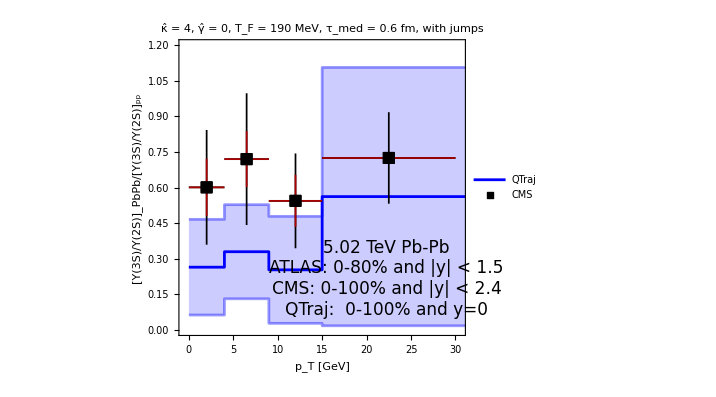

```mathematica
expPlot=ListPlot[{CMSdataStat,CMSdataSys},PlotRange->{{-0.5,30.5},{0,1}},IntervalMarkers->"Fences",IntervalMarkersStyle->{{Black,AbsoluteThickness[1.25]},{Darker[Red],AbsoluteThickness[1.25]}},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Black}],Black,Rectangle[]},ImageSize->11],Graphics[{EdgeForm[{AbsoluteThickness[1],Black}],Black,Rectangle[]},ImageSize->11]},ImageSize->500,PlotLegends->Placed[LineLegend[{"CMS",None},LabelStyle->16],{0.85,0.9}]];

theoryPlot=ListStepPlot[{qtrajResCenter,qtrajResMin,qtrajResMax} ,PlotRange->{{-0.5,30.5},{0,1.2}},PlotStyle->{{plotColor,AbsoluteThickness[2]},{plotColor,Opacity[0.4],AbsoluteThickness[2]},{plotColor,Opacity[0.4],AbsoluteThickness[2]}},FrameLabel->{"p_T [GeV]","[Υ(3S)/Υ(2S)]_PbPb/[Υ(3S)/Υ(2S)]_pp"},PlotLegends->Placed[LineLegend[{Style["QTraj",17]},LegendMarkerSize->{20,11}],{0.8575,0.82}],Epilog->Inset[Style["5.02 TeV Pb-Pb\nATLAS: 0-80% and |y| < 1.5\nCMS: 0-100% and |y| < 2.4\nQTraj:  0-100% and y=0",17,TextAlignment->Left],{22.25,0.215}],ImageSize->530, Filling->{2->{3}}];

doubleRatioPTPlot=Show[theoryPlot,expPlot,ImageSize->530,PlotLabel->Style[labelMap[dataDir],18]]
```

```mathematica
Export[wd<>"/figures/ratio-3s2s-vspt-"<>figureNameMap[dataDir]<>".pdf",doubleRatioPTPlot]
```

/home/sawin/Desktop/CMS_Bottomonia/bottomonia_PbPb5TeV/5 TeV/HNM/figures/ratio-3s2s-vspt-lhc-octet.pdf

```mathematica
doubleratio3s2svpt = qtrajResC;
fileName = wd<>"/figures/ratio-3s2s-vspt-"<>figureNameMap[dataDir]<>".m";
If[FileExistsQ[fileName],DeleteFile[fileName]];
Save[fileName,doubleratio3s2svpt]
```

## Results as a function of y averaged over centrality and p_T (with feed down)

#### Setup

```mathematica
getWeight[x_] := pFunction[cVsBInt[x[[1,1]]]]
```

```mathematica
mapWithWeight[x_] := Join[ pFunction[cVsBInt[x[[1,1]]]]*splitHyperfine[ x[[2]][[1;;6]] ],{x[[2,7]]}]
```

```mathematica
selectWeights[ymin_,ymax_]:=getWeight/@ Select[rawData,#[[1,7]]≥ymin&&#[[1,7]]≤ymax&]
```

```mathematica
selectYweighted[ymin_,ymax_]:=mapWithWeight/@ Select[rawData,#[[1,7]]≥ymin&&#[[1,7]]≤ymax&]
```

```mathematica
weightedList[ymin_,ymax_]:=Module[{wtm,res},
wtm = Mean[selectWeights[ymin,ymax]];
res = selectYweighted[ymin,ymax];
MapThread[Append,{res[[All,1;;9]]/wtm,res[[All,-1]]}]
]
```

```mathematica
nAAavgVsY[ymin_,ymax_]:= Module[{wl,num,qweights},
wl=weightedList[ymin,ymax];
qweights = wl[[All,-1]];
num = qweights //Total;
Transpose[wl[[All,1;;9]]].qweights/num
]
```

```mathematica
nAAsdevVsY[ymin_,ymax_]:=Module[{wl},
wl = weightedList[ymin,ymax];
StandardDeviation[wl]/Sqrt[Length[wl]]
]
nAAVsY[ymin_,ymax_]:=Module[{avg,err},
avg = nAAavgVsY[ymin,ymax];
err= nAAsdevVsY[ymin,ymax];
ParallelTable[Around[avg[[i]],err[[i]]]sigmas[[i]],{i,1,9}]
]
```

#### Plots

```mathematica
binwidth=1;
ymax = 6.5;
naavsyData=Table[Join[{x+binwidth/2},feeddownMatrix.nAAVsY[x,x+binwidth]/feeddownMatrix.sigmas],{x,-ymax,ymax-binwidth,binwidth}]//N
```

Part::partw: Part 7 of {0,-0.00755836,-1.03341,0,2.98241,5.57877} does not exist.

Part::partw: Part 7 of {0,-0.0297382,4.19082,0,11.2368,0.614328} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

StandardDeviation::shlen: The argument {} should have at least two elements.

Power::infy: Infinite expression 1/0 encountered.

```mathematica
pointMap[x_]:= {x[[1]],Around[x[[2]],x[[3]]]};
naa1s =naavsyData[[All,{1,2}]] ;
naa2s = naavsyData[[All,{1,3}]] ;
naa3s = naavsyData[[All,{1,7}]] ;

(* Symmetrize data *)
myMap[x_] := Around[x[[1]],x[[2]]/Sqrt[2]]
naa1s=Transpose[{naa1s[[All,1]],myMap/@((naa1s+Reverse[naa1s])/2)[[All,2]]}];
naa2s=Transpose[{naa1s[[All,1]],myMap/@((naa2s+Reverse[naa2s])/2)[[All,2]]}];
naa3s=Transpose[{naa1s[[All,1]],myMap/@((naa3s+Reverse[naa3s])/2)[[All,2]]}];
binsBoundaries=naavsyData[[All,1]];
```

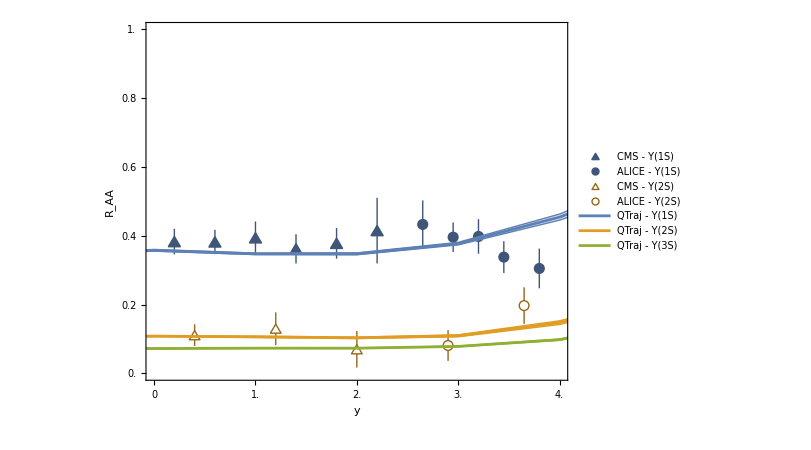

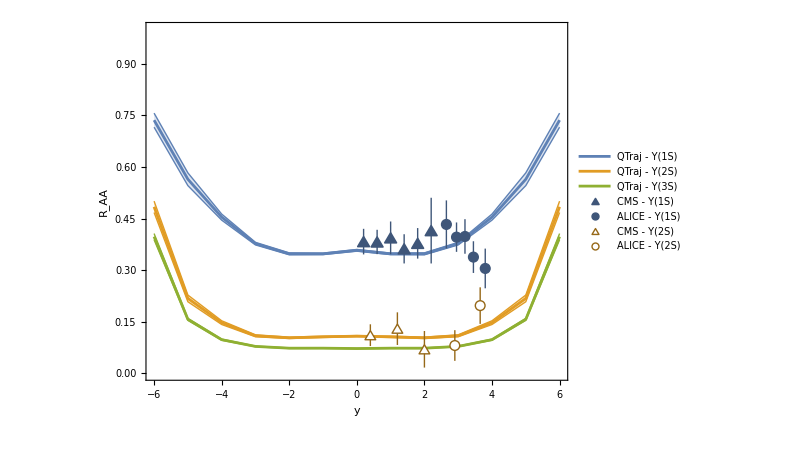

```mathematica
yPlot=ListPlot[{naa1s,naa2s,naa3s},Joined->True,InterpolationOrder->1,Frame->True,Axes->False,ImageSize->600,PlotMarkers->None,IntervalMarkers->"Bands",FrameLabel->{"y","R_AA"},PlotLegends->Placed[LineLegend[{Style["QTraj - Υ(1S)",16],Style["QTraj - Υ(2S)",16],Style["QTraj - Υ(3S)",16]},LegendMarkerSize->{{47,15}}],{0.2,0.83}],PlotRange->{0,1}];
yPlotWithExp=Show[expPlotY,yPlot]
Show[yPlot,expPlotY]
```

```mathematica
Export[wd<>"/figures/raavsy-"<>figureNameMap[dataDir]<>".pdf",yPlotWithExp]
```

/home/sawin/Desktop/Bottomonia_AA/LHC/5 TeV/HNM/figures/raavsy-lhc-3d.pdf

```mathematica
raavsy={naa1s,naa2s,naa3s};
Save[wd<>"/figures/raavsy-"<>figureNameMap[dataDir]<>".m",raavsy]
```

```mathematica
ResMin1S= Transpose[{binsBoundaries,Min/@mapInterval/@naa1s[[All,2]]}]; (* Prepare for liststepplot *)
ResCenter1S= Transpose[{binsBoundaries,mapValue/@naa1s[[All,2]]}]; (* Prepare for liststepplot *)
ResMax1S= Transpose[{binsBoundaries,Max/@mapInterval/@naa1s[[All,2]]}]; (* Prepare for liststepplot *)

ResMin2S= Transpose[{binsBoundaries,Min/@mapInterval/@naa2s[[All,2]]}]; (* Prepare for liststepplot *)
ResCenter2S= Transpose[{binsBoundaries,mapValue/@naa2s[[All,2]]}]; (* Prepare for liststepplot *)
ResMax2S= Transpose[{binsBoundaries,Max/@mapInterval/@naa2s[[All,2]]}]; (* Prepare for liststepplot *)

ResMin3S= Transpose[{binsBoundaries,Min/@mapInterval/@naa3s[[All,2]]}]; (* Prepare for liststepplot *)
ResCenter3S= Transpose[{binsBoundaries,mapValue/@naa3s[[All,2]]}]; (* Prepare for liststepplot *)
ResMax3S= Transpose[{binsBoundaries,Max/@mapInterval/@naa3s[[All,2]]}]; (* Prepare for liststepplot *)
```

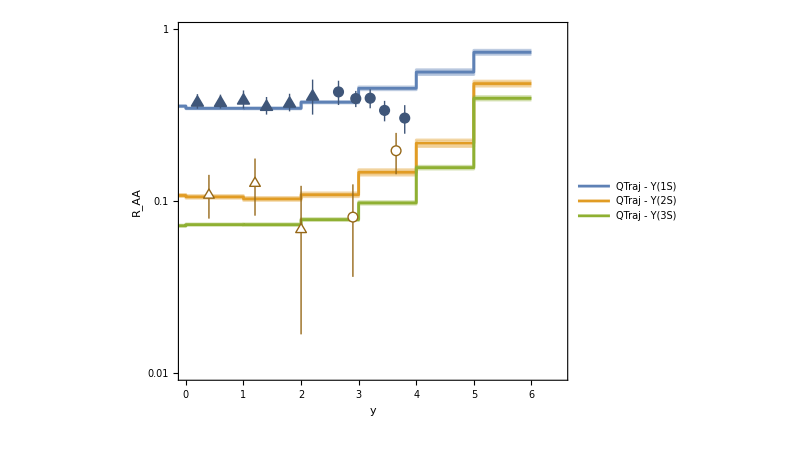

```mathematica
yPlotLog1=ListStepPlot[{ResCenter1S,ResMin1S,ResMax1S,ResCenter2S,ResMin2S,ResMax2S,ResCenter3S,ResMin3S,ResMax3S},Left,ScalingFunctions->{None,"Log"},Joined->True,Frame->True,Axes->False,ImageSize->600,PlotMarkers->None,IntervalMarkers->"Bars",FrameLabel->{"y","R_AA"},PlotStyle->{{plotColor1,AbsoluteThickness[2]},{plotColor1,Opacity[0.4],AbsoluteThickness[2]},{plotColor1,Opacity[0.4],AbsoluteThickness[2]},{plotColor2,AbsoluteThickness[2]},{plotColor2,Opacity[0.4],AbsoluteThickness[2]},{plotColor2,Opacity[0.4],AbsoluteThickness[2]},{plotColor3,AbsoluteThickness[2]},{plotColor3,Opacity[0.4],AbsoluteThickness[2]},{plotColor3,Opacity[0.4],AbsoluteThickness[2]}},Filling->{2->{3},5->{6},8->{9}},PlotLegends->Placed[LineLegend[{Style["QTraj - Υ(1S)",16],None,None,Style["QTraj - Υ(2S)",16],None,None,Style["QTraj - Υ(3S)",16],None,None},LegendMarkerSize->{{47,15}},LegendMargins->20],{Right,Bottom}],PlotRange->{{0,6.5},{0.01,1}}];
yPlotLog=Show[yPlotLog1,expPlotYLog]
```

```mathematica
Export[wd<>"/figures/raavsy-log-binned-"<>figureNameMap[dataDir]<>".pdf",yPlotLog]
```

/home/sawin/Desktop/Bottomonia_AA/LHC/5 TeV/HNM/figures/raavsy-log-binned-lhc-3d.pdf

## Integrated results

```mathematica
raaRes1=feeddownMatrix.nAAVsPT[0,40,0,1]/feeddownMatrix.sigmas
```

{0.37700.0022,0.12200.0016,0.2460.018,0.2450.018,0.2450.018,0.08670.0006,0.2040.011,0.2040.011,0.2040.011}

```mathematica
res1s =raaRes1[[1]]
res2s = raaRes1[[2]]
res3s = raaRes1[[6]]
```

0.37700.0022

0.12200.0016

0.08670.0006

```mathematica
res3s/res2s
```

0.7110.011

```mathematica
CMS1s1 = Around[0.376,0.013];
CMS1s2 = Around[0.376,0.035];
CMS2s1 = Around[0.115 ,0.007];
CMS2s2 = Around[0.115 ,0.007];
CMS3s1 = Around[0.081, 0.015];
CMS3s2 = Around[0.081, 0.012];
CMS2s1sRatio1 = Around[0.308, 0.055];
CMS2s1sRatio2 = Around[0.308, 0.001];
CMS3s2sRatio1 = Around[0.709, 0.135];
CMS3s2sRatio2 = Around[0.709, 0.078];
```

```mathematica
ALICE1s1 = Around[0.37,0.02];
ALICE1s2 = Around[0.37,0.03];
ALICE2s1 = Around[0.10,0.04];
ALICE2s2 = Around[0.10,0.02];
ALICE2s1sRatio1 = Around[0.28, 0.12];
ALICE2s1sRatio2 = Around[0.28, 0.06];
```

```mathematica
ATLAS1s1 = Around[0.32,0.02];
ATLAS1s2 = Around[0.32,0.05];
ATLAS2s1 = Around[0.11,0.04];
ATLAS2s2 = Around[0.11,0.04];
ATLAS2s1sRatio1 = Around[0.35, 0.12];
ATLAS2s1sRatio2 = Around[0.35, 0.12];
```

```mathematica
myData1={{{1,res1s},{2,res2s},{3,res3s}},
{{1.1,CMS1s1},{2.1,CMS2s1},{3.1,CMS3s1}},
{{1.1,CMS1s2},{2.1,CMS2s2},{3.1,CMS3s2}},
{{1.2,ALICE1s1},{2.2,ALICE2s1}},
{{1.2,ALICE1s2},{2.2,ALICE2s2}},
{{1.3,ATLAS1s1},{2.3,ATLAS2s1}},
{{1.3,ATLAS1s2},{2.3,ATLAS2s2}}};
myData2={{{1,res2s/res1s}},
{{1.1,CMS2s1sRatio1}},
{{1.1,CMS2s1sRatio2}},
{{1.2,ALICE2s1sRatio1}},
{{1.2,ALICE2s1sRatio2}},
{{1.3,ATLAS2s1sRatio1}},
{{1.3,ATLAS2s1sRatio2}},
{{2,res3s/res2s}},
{{2.1,CMS3s2sRatio1}},
{{2.1,CMS3s2sRatio2}}};
```

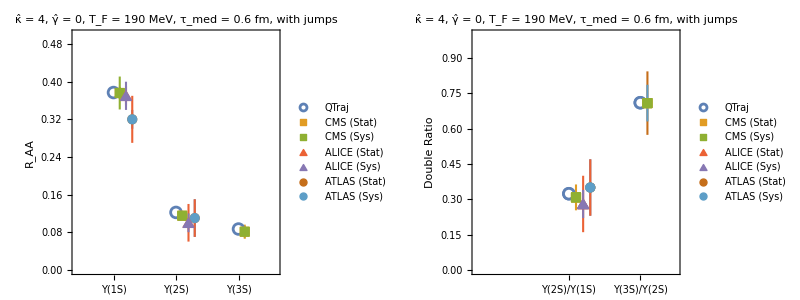

```mathematica
plotColor1= ColorData[97,"ColorList"][[1]];
plotColor2= ColorData[97,"ColorList"][[2]];
plotColor3= ColorData[97,"ColorList"][[3]];
plotColor4= ColorData[97,"ColorList"][[4]];
plotColor5= ColorData[97,"ColorList"][[5]];
plotColor6= ColorData[97,"ColorList"][[6]];
plotColor7= ColorData[97,"ColorList"][[7]];
p1=ListPlot[myData1,PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[2],plotColor1}],White,Disk[]},ImageSize->11],
Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor2}],plotColor2,Rectangle[]},ImageSize->9],Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor3}],plotColor3,Rectangle[]},ImageSize->9],Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor4}],plotColor4,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->11],Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor5}],plotColor5,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->11],Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor6}],plotColor6,Disk[]},ImageSize->9],Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor7}],plotColor7,Disk[]},ImageSize->9]},IntervalMarkersStyle->{{plotColor1,AbsoluteThickness[1.5]},{plotColor2,AbsoluteThickness[1.5]},{plotColor3,AbsoluteThickness[1.5]},{plotColor4,AbsoluteThickness[1.5]},{plotColor5,AbsoluteThickness[1.5]},{plotColor1,AbsoluteThickness[1.5]},{plotColor4,AbsoluteThickness[1.5]},{plotColor5,AbsoluteThickness[1.5]}},FrameTicks->{{Automatic,Automatic},{{{1,"Υ(1S)"},{2 ,"Υ(2S)"},{3,"Υ(3S)"}},None}},FrameLabel->{None,"R_AA"},BaseStyle->17,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial",{AbsoluteThickness[framewidth]}],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial",{AbsoluteThickness[framewidth]}]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[framewidth]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[framewidth]]},AspectRatio->0.8,PlotRange->{{0.4,3.6},{0,0.5}},PlotLegends->Placed[LineLegend[{"QTraj","CMS (Stat)","CMS (Sys)","ALICE (Stat)","ALICE (Sys)","ATLAS (Stat)","ATLAS (Sys)"},LegendMargins->10,LabelStyle->15],{Right,Top}],PlotLabel->Style[labelMap[dataDir],13],ImageSize->450];

p2=ListPlot[myData2,IntervalMarkersStyle->{{plotColor1,AbsoluteThickness[1.5]},{plotColor2,AbsoluteThickness[1.5]},{plotColor3,AbsoluteThickness[1.5]},{plotColor4,AbsoluteThickness[1.5]},{plotColor5,AbsoluteThickness[1.5]},{plotColor1,AbsoluteThickness[1.5]},{plotColor4,AbsoluteThickness[1.5]},{plotColor5,AbsoluteThickness[1.5]},{plotColor6,AbsoluteThickness[1.5]},{plotColor7,AbsoluteThickness[1.5]},{plotColor1,AbsoluteThickness[1.5]},{plotColor2,AbsoluteThickness[1.5]},{plotColor3,AbsoluteThickness[1.5]}},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[2],plotColor1}],White,Disk[]},ImageSize->11],
Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor2}],plotColor2,Rectangle[]},ImageSize->9],Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor3}],plotColor3,Rectangle[]},ImageSize->9],Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor4}],plotColor4,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->11],Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor5}],plotColor5,Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->11],Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor6}],plotColor6,Disk[]},ImageSize->9],Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor7}],plotColor7,Disk[]},ImageSize->9],Graphics[{EdgeForm[{AbsoluteThickness[2],plotColor1}],White,Disk[]},ImageSize->11],Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor2}],plotColor2,Rectangle[]},ImageSize->9],Graphics[{EdgeForm[{AbsoluteThickness[1],plotColor3}],plotColor3,Rectangle[]},ImageSize->9]},Frame->True,PlotRange->{{-0.3,2.5},{0,1}},FrameTicks->{{Automatic,Automatic},{{{1,"Υ(2S)/Υ(1S)"},{2,"Υ(3S)/Υ(2S)"}},Automatic}},FrameLabel->{None,"Double Ratio"},BaseStyle->17,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial",{AbsoluteThickness[framewidth]}],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Arial",{AbsoluteThickness[framewidth]}]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[framewidth]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Arial",AbsoluteThickness[framewidth]]},AspectRatio->0.8,PlotLegends->Placed[LineLegend[{"QTraj","CMS (Stat)","CMS (Sys)","ALICE (Stat)","ALICE (Sys)","ATLAS (Stat)","ATLAS (Sys)"},LegendMargins->10,LabelStyle->15],{Left,Top}],PlotLabel->Style[labelMap[dataDir],13],ImageSize->450];

intPlot=Grid[{{p1,p2}},Spacings->1.5]
```

```mathematica
Export[wd<>"/figures/integrated-"<>figureNameMap[dataDir]<>".pdf",intPlot]
```

/home/sawin/Desktop/Bottomonia_AA/LHC/5 TeV/HNM/figures/integrated-lhc-3d.pdf

## Integrated v_n (with p_T and centrality cuts; with feed down + proper centrality weighting)

```mathematica
ptbinCenters = {Around[3/2,3/2],Around[9/2,3/2],Around[8,2],Around[30,20]}
```

{1.51.5,4.51.5,8.02.0,30.20.}

```mathematica
vNavg[n_,rAA_,phiVals_] := Total[rAA Cos[n phiVals]]/Total[rAA]
vNstderr[n_,rAA_,phiVals_] := StandardDeviation[rAA Cos[n phiVals]/Mean[rAA]]/Sqrt[Length[rAA]]
feeddownMap[x_] := pFunction[cVsBInt[x[[1,1]]]]feeddownMatrix.(splitHyperfine[x[[2]][[1;;6]]]*x[[2,7]]*sigmas)
```

```mathematica
computeVn[n_,ptmin_,ptmax_,cmin_,cmax_]:=Module[
{myEvents,rAAvec,rAA1s,rAA2s,rAA3s,phiVals,phiValsP,den,metadata,metadataP,i,data},
myEvents=Select[rawData,cVsBInt[#[[1,1]]]≥ cmin &&cVsBInt[#[[1,1]]]≤ cmax&& #[[1,5]]≥ptmin&&#[[1,5]]<=ptmax&];
rAAvec=feeddownMap /@ myEvents;
den =feeddownMatrix.sigmas;
rAA1s = rAAvec[[All,1]]/den[[1]];
rAA2s = rAAvec[[All,2]]/den[[2]];
rAA3s = rAAvec[[All,6]]/den[[6]];
phiVals=myEvents[[All,1,6]];
{Around[vNavg[n,rAA1s,phiVals],vNstderr[n,rAA1s,phiVals]],
Around[vNavg[n,rAA2s,phiVals],vNstderr[n,rAA2s,phiVals]],
Around[vNavg[n,rAA3s,phiVals],vNstderr[n,rAA3s,phiVals]]}
]
```

```mathematica
computeVn[2,0,40,0,0.1]
```

{0.0040.010,0.0080.025,0.0100.013}

### Compare to Experimental data!

#### Figure 2a from CMS Paper

```mathematica
expDataY1sv2 = {
{Around[20,10],Around[0.0052561,Sqrt[0.0159649^2+0.00527002^2]]},
{Around[40,10],Around[0.024584,Sqrt[0.0181968^2+0.00933611^2]]},
{Around[70,20],Around[-0.0161228,Sqrt[0.0318923^2+0.0108534^2]]},
{110, Around[0.00700736,Sqrt[0.0111854^2+0.0052784^2]]}
}
```

{{20.10.,0.0050.017},{40.10.,0.0250.020},{70.20.,-0.0160.034},{110,0.0070.012}}

```mathematica
cBins2a = {Around[20,10],Around[40,10],Around[70,20],110};
```

```mathematica
res1030allpt=computeVn[2,0,40,0.1,0.3];
res3050allpt=computeVn[2,0,40,0.3,0.5];
res5090allpt=computeVn[2,0,40,0.5,0.9];
res1090allpt=computeVn[2,0,40,0.1,0.9];
allResultsPT = {res1030allpt,res3050allpt,res5090allpt,res1090allpt}
```

{{0.0060.011,-0.0130.029,0.0230.014},{0.0090.011,0.0280.024,0.0390.011},{0.0210.008,0.0230.006,0.0160.004},{0.0110.006,0.0140.010,0.0220.005}}

```mathematica
theoryData1s= Partition[Riffle[cBins2a,allResultsPT[[All,1]]],2]
```

{{20.10.,0.0060.011},{40.10.,0.0090.011},{70.20.,0.0210.008},{110,0.0110.006}}

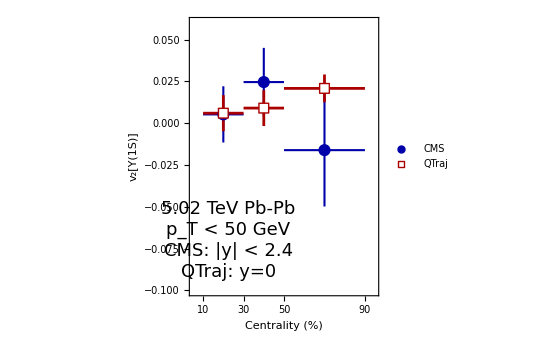
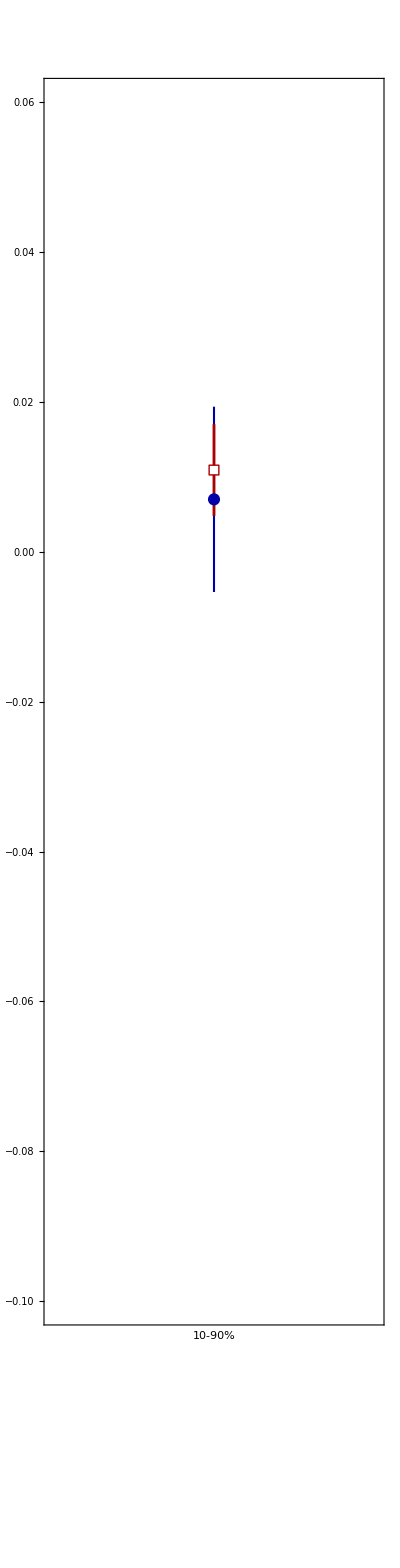
κ̂ = 4, γ̂ = 0, T_F = 190 MeV, τ_med = 0.6 fm, with jumps | 
-Graphics- | -Graphics-

```mathematica
myTicks = {{10,"10"},{30,"30"},{50,"50"},{90,"90"}};p1=ListPlot[{expDataY1sv2,theoryData1s},PlotRange->{{5,95},{-0.10,0.06}},FrameTicks->{{Automatic,Automatic},{myTicks,Automatic}},IntervalMarkers->"Fences",IntervalMarkersStyle->{{AbsoluteThickness[1.5],Darker[Blue]},{AbsoluteThickness[2],Darker[Red]},{AbsoluteThickness[2],Darker[Green]}},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Blue]}],Darker[Blue],Disk[]},ImageSize->11],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Red]}],White,Rectangle[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Green]}],Darker[Green],Disk[]},ImageSize->11]},FrameLabel->{"Centrality (%)","v_2[Υ(1S)]"},ImageSize->{Automatic,450},PlotLegends->Placed[LineLegend[{"CMS","QTraj"},LabelStyle->20],{0.77,0.90}],AspectRatio->7/8,Epilog->Inset[Style["5.02 TeV Pb-Pb\np_T < 50 GeV\nCMS: |y| < 2.4\nQTraj: y=0",18,TextAlignment->Left],{22.5,-0.07}],ImagePadding->{{90,0},{60,10}},Axes->True];
p2=ListPlot[{expDataY1sv2,theoryData1s},PlotRange->{{100,120},{-0.10,0.06}},FrameTicks->{{Automatic,Automatic},{None,None}},IntervalMarkers->"Fences",IntervalMarkersStyle->{{AbsoluteThickness[1.5],Darker[Blue]},{AbsoluteThickness[2],Darker[Red]},{AbsoluteThickness[2],Darker[Green]}},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Blue]}],Darker[Blue],Disk[]},ImageSize->11],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Red]}],White,Rectangle[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Green]}],Darker[Green],Disk[]},ImageSize->11]},FrameLabel->{Style["10-90%",18],""},ImageSize->{Automatic,450},AspectRatio->4,ImagePadding->{{1,10},{60,10}},Axes->True];
CMSFig2plot = Grid[{{Text[Style["                                "<>labelMap[dataDir],18]]},{p1,p2}},Spacings->{-0.13,0}]
```

```mathematica
Export[wd<>"/figures/cmsfig2-"<>figureNameMap[dataDir]<>".pdf",CMSFig2plot]
```

/home/sawin/Desktop/Bottomonia_AA/LHC/5 TeV/HNM/figures/cmsfig2-lhc-3d.pdf

```mathematica
v21svsc = theoryData1s;
fileName = wd<>"/figures/cmsfig2-"<>figureNameMap[dataDir]<>".m";
If[FileExistsQ[fileName],DeleteFile[fileName]];
Save[fileName,v21svsc]
```

```mathematica
cBins2a = {Around[20,10],Around[40,10],Around[70,20],110};
```

```mathematica
(*Calculate V1 -- Directed Flow*)
```

```mathematica
res1030allptv1=computeVn[1,0,40,0.1,0.3];
res3050allptv1=computeVn[1,0,40,0.3,0.5];
res5090allptv1=computeVn[1,0,40,0.5,0.9];
res1090allptv1=computeVn[1,0,40,0.1,0.9];
allResultsPTv1 = {res1030allptv1,res3050allptv1,res5090allptv1,res1090allptv1};
theoryData1sv1= Partition[Riffle[cBins2a,allResultsPTv1[[All,1]]],2];
theoryData2sv1= Partition[Riffle[cBins2a,allResultsPTv1[[All,2]]],2];
theoryData3sv1= Partition[Riffle[cBins2a,allResultsPTv1[[All,3]]],2];
```

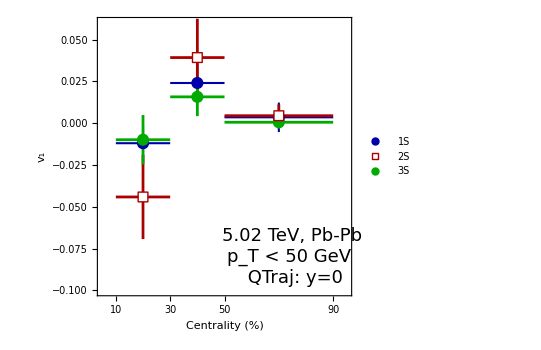

```mathematica
ListPlot[{theoryData1sv1,theoryData2sv1,theoryData3sv1},PlotRange->{{5,95},{-0.10,0.06}},FrameTicks->{{Automatic,Automatic},{myTicks,Automatic}},IntervalMarkers->"Fences",IntervalMarkersStyle->{{AbsoluteThickness[1.5],Darker[Blue]},{AbsoluteThickness[2],Darker[Red]},{AbsoluteThickness[2],Darker[Green]}},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Blue]}],Darker[Blue],Disk[]},ImageSize->11],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Red]}],White,Rectangle[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Green]}],Darker[Green],Disk[]},ImageSize->11]},FrameLabel->{"Centrality (%)","v_1"},ImageSize->{Automatic,450},PlotLegends->Placed[LineLegend[{"1S","2S","3S"},LabelStyle->20],{0.77,0.85}],AspectRatio->7/8,Epilog->Inset[Style["5.02 TeV, Pb-Pb\np_T < 50 GeV \n QTraj: y=0",18,TextAlignment->Left],{75,-0.08}],ImagePadding->{{90,0},{60,10}},Axes->True]
```

#### Figure 2a from CMS Paper - Predictions for 2s and 3s.

```mathematica
theoryData2s= Partition[Riffle[cBins2a,allResultsPT[[All,2]]],2]
theoryData3s= Partition[Riffle[cBins2a,allResultsPT[[All,3]]],2]
```

{{20.10.,-0.0130.029},{40.10.,0.0280.024},{70.20.,0.0230.006},{110,0.0140.010}}

{{20.10.,0.0230.014},{40.10.,0.0390.011},{70.20.,0.0160.004},{110,0.0220.005}}

```mathematica
cmsY2sPt={{110,Around[-0.0629946,Sqrt[0.084861^2+0.0371522^2]]}}
```

{{110,-0.060.09}}

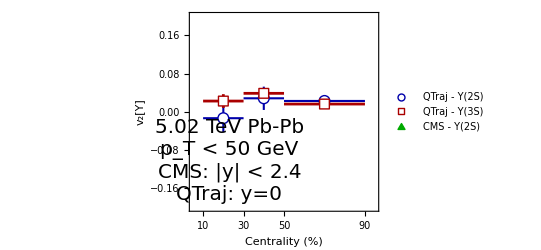
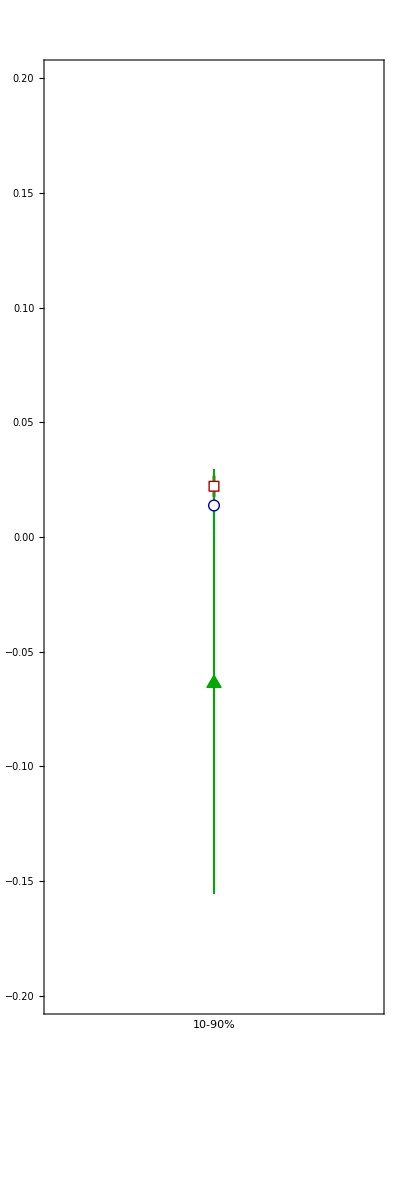
κ̂ = 4, γ̂ = 0, T_F = 190 MeV, τ_med = 0.6 fm, with jumps | 
-Graphics- | -Graphics-

```mathematica
myTicks = {{10,"10"},{30,"30"},{50,"50"},{90,"90"}};p1=ListPlot[{theoryData2s,theoryData3s,cmsY2sPt },PlotRange->{{5,95},{-0.20,0.20}},FrameTicks->{{Automatic,Automatic},{myTicks,Automatic}},IntervalMarkers->"Fences",IntervalMarkersStyle->{{AbsoluteThickness[1.5],Darker[Blue]},{AbsoluteThickness[2],Darker[Red]},{AbsoluteThickness[2],Darker[Green]}},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Blue]}],White,Disk[]},ImageSize->11],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Red]}],White,Rectangle[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Green]}],Darker[Green],Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->11]},FrameLabel->{"Centrality (%)","v_2[Υ]"},ImageSize->{Automatic,350},PlotLegends->Placed[LineLegend[{"QTraj - Υ(2S)","QTraj - Υ(3S)","CMS - Υ(2S)"},LabelStyle->20,LegendMarkerSize->13],{0.7,0.28}],AspectRatio->5/8,Epilog->Inset[Style["5.02 TeV Pb-Pb\np_T < 50 GeV\nCMS: |y| < 2.4\nQTraj: y=0",20,TextAlignment->Left],{23,-0.1025}],ImagePadding->{{90,0},{60,10}},Axes->True];
p2=ListPlot[{theoryData2s,theoryData3s,cmsY2sPt },PlotRange->{{100,120},{-0.20,0.20}},FrameTicks->{{Automatic,Automatic},{None,None}},IntervalMarkers->"Fences",IntervalMarkersStyle->{{AbsoluteThickness[1.5],Darker[Blue]},{AbsoluteThickness[2],Darker[Red]},{AbsoluteThickness[1.5],Darker[Green]}},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Blue]}],White,Disk[]},ImageSize->11],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Red]}],White,Rectangle[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Green]}],Darker[Green],Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->14]},FrameLabel->{"10-90%",""},ImageSize->{Automatic,350},AspectRatio->3,ImagePadding->{{1,10},{60,10}},Axes->True];
CMSFig2plotExcited = Grid[{{Text[Style["                                "<>labelMap[dataDir],18]]},{p1,p2}},Spacings->{-0.13,0}]
```

```mathematica
Export[wd<>"/figures/cmsfig2excited-"<>figureNameMap[dataDir]<>".pdf",CMSFig2plotExcited ]
```

/home/sawin/Desktop/Bottomonia_AA/LHC/5 TeV/HNM/figures/cmsfig2excited-lhc-3d.pdf

```mathematica
v22s3svsc = theoryData1s;
fileName = wd<>"/figures/cmsfig2excited-"<>figureNameMap[dataDir]<>".m";
If[FileExistsQ[fileName],DeleteFile[fileName]];
Save[fileName,v22s3svsc]
```

#### Figure 2b from CMS Paper

```mathematica
res10901=computeVn[2,0,3,0.1,0.9];
res10902=computeVn[2,3,6,0.1,0.9];
res10903=computeVn[2,6,10,0.1,0.9];
res10904=computeVn[2,10,40,0.1,0.9];
allResults = {res10901,res10902,res10903,res10904}
```

{{-0.0130.016,-0.0360.035,0.0200.017},{0.0280.013,0.0460.026,0.0140.011},{-0.0070.014,-0.0320.024,0.0080.010},{0.0180.009,0.0330.012,0.0320.007}}

```mathematica
cmsDataVpt =Partition[Riffle[ptbinCenters, {
Around[0.0043246,Sqrt[0.0187855^2+0.0114855^2]],
Around[-0.0179325,Sqrt[0.019071^2+0.00452821^2]],
Around[0.0579537,Sqrt[0.0225032^2+0.003664^2]],
Around[0.0180797,Sqrt[0.0208218^2+0.00669609^2]]}],2]
```

{{1.51.5,0.0040.022},{4.51.5,-0.0180.020},{8.02.0,0.0580.023},{30.20.,0.0180.022}}

```mathematica
Partition[Riffle[ptbinCenters,allResults[[All,1]]],2]
```

{{1.51.5,-0.0130.016},{4.51.5,0.0280.013},{8.02.0,-0.0070.014},{30.20.,0.0180.009}}

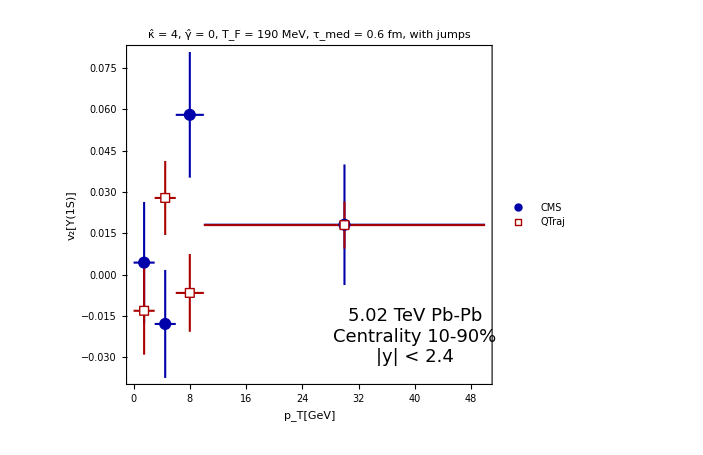

```mathematica
CMSFig2bplot = ListPlot[{cmsDataVpt,Partition[Riffle[ptbinCenters,allResults[[All,1]]],2]},IntervalMarkers->"Fences",IntervalMarkersStyle->{{AbsoluteThickness[1.5],Darker[Blue]},{AbsoluteThickness[1.5],Darker[Red]},{AbsoluteThickness[1.2],Darker[Green]}},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Blue]}],Darker[Blue],Disk[]},ImageSize->11],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Red]}],White,Rectangle[]},ImageSize->9],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Green]}],Darker[Green],Disk[]},ImageSize->11]},FrameLabel->{"p_T[GeV]","v_2[Υ(1S)]"},ImageSize->520,PlotLegends->Placed[LineLegend[{"CMS","QTraj"},LabelStyle->18],{0.8,0.84}],Epilog->Inset[Style["5.02 TeV Pb-Pb\nCentrality 10-90%\n|y| < 2.4",18,TextAlignment->Left],{40,-0.0225}],AspectRatio->7/8,PlotLabel->Style[labelMap[dataDir],18]]
```

```mathematica
Export[wd<>"/figures/cmsfig2b-"<>figureNameMap[dataDir]<>".pdf",CMSFig2bplot ]
```

/home/sawin/Desktop/Bottomonia_AA/LHC/5 TeV/HNM/figures/cmsfig2b-lhc-3d.pdf

```mathematica
v21svpt=Partition[Riffle[ptbinCenters,allResults[[All,1]]],2];
fileName = wd<>"/figures/cmsfig2b-"<>figureNameMap[dataDir]<>".m";
If[FileExistsQ[fileName],DeleteFile[fileName]];
Save[fileName,v21svpt]
```

#### v2[2S]/v2[1S]

```mathematica
expDataR21 ={{4.5, Around[2.3027415,4.463014-2.3027415]},{8, Around[1.3644664,4.5003457-1.3644664]},{30, Around[2.9477441,6.0486646-2.9477441]}}
```

{{4.5,2.32.2},{8,1.43.1},{30,2.93.1}}

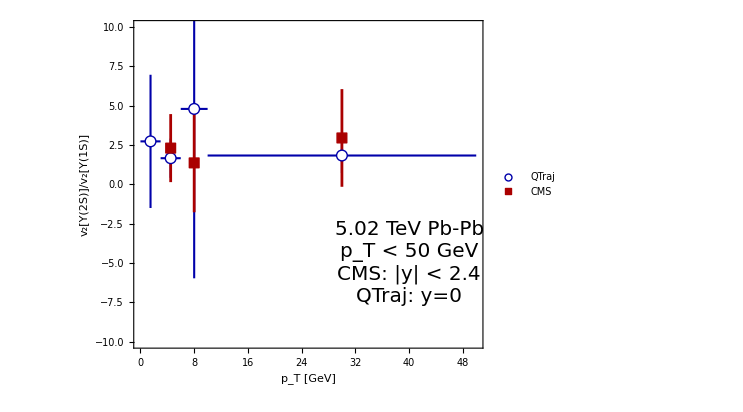

```mathematica
ListPlot[{Partition[Riffle[ptbinCenters,allResults[[All,2]]/allResults[[All,1]]],2],expDataR21},PlotStyle->Thick,PlotRange->{-10,10},IntervalMarkers->"Fences",IntervalMarkersStyle->{{AbsoluteThickness[1.5],Darker[Blue]},{AbsoluteThickness[2],Darker[Red]},{AbsoluteThickness[2],Darker[Green]}},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Blue]}],White,Disk[]},ImageSize->11],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Red]}],Darker[Red],Rectangle[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Green]}],Darker[Green],Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->11]},FrameLabel->{"p_T [GeV]","v_2[Υ(2S)]/v_2[Υ(1S)]"},ImageSize->550,PlotLegends->Placed[LineLegend[{"QTraj","CMS"},LabelStyle->20,LegendMarkerSize->12,LegendMargins->20],{Right,Top}],AspectRatio->3/4,Epilog->Inset[Style["5.02 TeV Pb-Pb\np_T < 50 GeV\nCMS: |y| < 2.4\nQTraj: y=0",20,TextAlignment->Left],{40,-5}],ImagePadding->{{90,0},{60,10}}]
```

#### Figure 3a from CMS Paper

```mathematica
CMSfig3a = Partition[Riffle[ptbinCenters,{
Around[-0.00638822,Sqrt[0.0279342^2+0.0151051^2]],
Around[-0.0169761,Sqrt[0.0251838^2+0.0129453^2]],
Around[0.0646497,Sqrt[0.0325005^2+0.0070688^2]],
Around[0.0225499,Sqrt[0.0286433^2+0.0119792^2]]}],2]
```

{{1.51.5,-0.0060.032},{4.51.5,-0.0170.028},{8.02.0,0.0650.033},{30.20.,0.0230.031}}

```mathematica
res10301=computeVn[2,0,3,0.1,0.3];
res10302=computeVn[2,3,6,0.1,0.3];
res10303=computeVn[2,6,10,0.1,0.3];
res10304=computeVn[2,10,40,0.1,0.3];
allResults1030 = {res10301,res10302,res10303,res10304}
```

{{-0.0300.027,-0.200.11,0.020.06},{0.0520.025,0.140.07,0.010.04},{-0.0180.025,-0.120.07,0.0050.030},{0.0070.015,0.0050.033,0.0340.019}}

```mathematica
panela=ListPlot[{CMSfig3a,Partition[Riffle[ptbinCenters,allResults1030[[All,1]]],2]},IntervalMarkers->"Fences",IntervalMarkersStyle->{{AbsoluteThickness[2],Darker[Blue]},{AbsoluteThickness[2],Darker[Red]},{AbsoluteThickness[1.2],Darker[Green]}},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Blue]}],Darker[Blue],Disk[]},ImageSize->11],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Red]}],White,Rectangle[]},ImageSize->9],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Green]}],Darker[Green],Disk[]},ImageSize->11]},FrameLabel->{"p_T[GeV]","v_2[Υ(1S)]"},ImageSize->{Automatic,450},PlotLegends->Placed[LineLegend[{"CMS 2020","QTraj"},LabelStyle->18],{0.80,0.86}],PlotLabel->Style["(a) 10-30% Centrality",16],AspectRatio->7/8,ImagePadding->{{87,2},{60,2}},Epilog->Inset[Style["5.02 TeV Pb-Pb\n|y| < 2.4",18,TextAlignment->Right],{40,0.052}],Axes->True,PlotRange->{-0.06,0.1}];
```

#### Figure 3b from CMS Paper

```mathematica
CMSfig3b = Partition[Riffle[ptbinCenters,{
Around[0.0388375,Sqrt[0.0301701^2+0.00982201^2]],
Around[-0.00624462,Sqrt[0.0330022^2+0.0132499^2]],
Around[0.077756,Sqrt[0.0408395^2+0.0105044^2]],
Around[-0.00737962,Sqrt[0.0354003^2+0.0114622^2]]}],2]
```

{{1.51.5,0.0390.032},{4.51.5,0.000.04},{8.02.0,0.080.04},{30.20.,0.000.04}}

```mathematica
res30501=computeVn[2,0,3,0.3,0.5];
res30502=computeVn[2,3,6,0.3,0.5];
res30503=computeVn[2,6,10,0.3,0.5];
res30504=computeVn[2,10,40,0.3,0.5];
allResults3050= {res30501,res30502,res30503,res30504}
```

{{-0.0010.027,0.090.08,0.070.04},{0.0170.021,-0.020.08,0.0040.027},{-0.0290.024,-0.040.05,0.0120.023},{0.0290.016,0.0740.031,0.0580.015}}

```mathematica
panelb=ListPlot[{CMSfig3b,Partition[Riffle[ptbinCenters,allResults3050[[All,1]]],2]},IntervalMarkers->"Fences",IntervalMarkersStyle->{{AbsoluteThickness[2],Darker[Blue]},{AbsoluteThickness[2],Darker[Red]},{AbsoluteThickness[1.2],Darker[Green]}},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Blue]}],Darker[Blue],Disk[]},ImageSize->11],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Red]}],White,Rectangle[]},ImageSize->9],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Green]}],Darker[Green],Disk[]},ImageSize->11]},FrameLabel->{"p_T[GeV]",None},ImageSize->{Automatic,450},PlotLegends->Placed[LineLegend[{"CMS 2020","QTraj"},LabelStyle->18],{0.8,0.86}],Epilog->Inset[Style["5.02 TeV Pb-Pb\n|y| < 2.4",18,TextAlignment->Right],{40,0.052}],AspectRatio->7/8,PlotRange->{-0.06,0.1},FrameTicksStyle->{Directive[FontOpacity->0,FontSize->0],Automatic},ImagePadding->{{2,2},{60,2}},PlotLabel->Style["(b) 30-50% Centrality",16],Axes->True];
```

#### Figure 3c from CMS Paper

```mathematica
CMSfig3c = Partition[Riffle[ptbinCenters,{
Around[-0.0396625,Sqrt[0.0508687^2+0.0264666^2]],
Around[-0.0223604,Sqrt[0.0557153^2+0.0130196^2]],
Around[-0.0278458,Sqrt[0.0623273^2+0.0146513^2]],
Around[0.0826174,Sqrt[0.0680158^2+0.0251745^2]]}],2]
```

{{1.51.5,-0.040.06},{4.51.5,-0.020.06},{8.02.0,-0.030.06},{30.20.,0.080.07}}

```mathematica
res50901=computeVn[2,0,3,0.5,0.9];
res50902=computeVn[2,3,6,0.5,0.9];
res50903=computeVn[2,6,10,0.5,0.9];
res50904=computeVn[2,10,40,0.5,0.9];
allResults5090= {res50901,res50902,res50903,res50904}
```

{{0.0000.027,-0.0040.020,0.0060.013},{0.0000.017,0.0150.013,0.0170.008},{0.0350.019,0.0210.013,0.0080.007},{0.0260.012,0.0310.009,0.0220.005}}

```mathematica
panelc=ListPlot[{CMSfig3c,Partition[Riffle[ptbinCenters,allResults5090[[All,1]]],2]},IntervalMarkers->"Fences",IntervalMarkersStyle->{{AbsoluteThickness[2],Darker[Blue]},{AbsoluteThickness[2],Darker[Red]},{AbsoluteThickness[1.2],Darker[Green]}},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Blue]}],Darker[Blue],Disk[]},ImageSize->11],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Red]}],White,Rectangle[]},ImageSize->9],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Green]}],Darker[Green],Disk[]},ImageSize->11]},FrameLabel->{"p_T[GeV]","v_2[Υ(1S)]"},ImageSize->{Automatic,450},PlotLegends->Placed[LineLegend[{"CMS 2020","QTraj"},LabelStyle->18],{0.8,0.27}],Epilog->Inset[Style["5.02 TeV Pb-Pb\n|y| < 2.4",18,TextAlignment->Right],{40,-0.0425}],AspectRatio->7/8,PlotRange->{-0.06,0.1},
FrameTicksStyle->{Directive[FontOpacity->0,FontSize->0],Automatic},ImagePadding->{{2,100},{60,2}},PlotLabel->Style["(c) 50-90% Centrality",16],AspectRatio->7/8,Axes->True];
```

#### Figure 3 from CMS Paper (Combined a, b, and c)

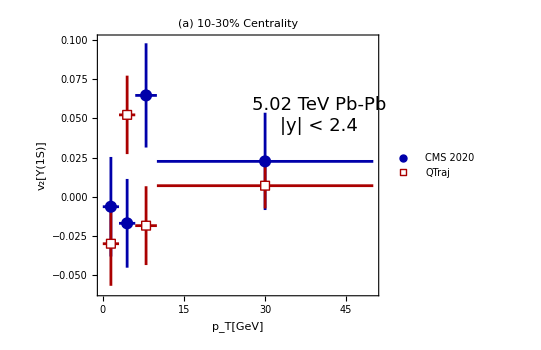
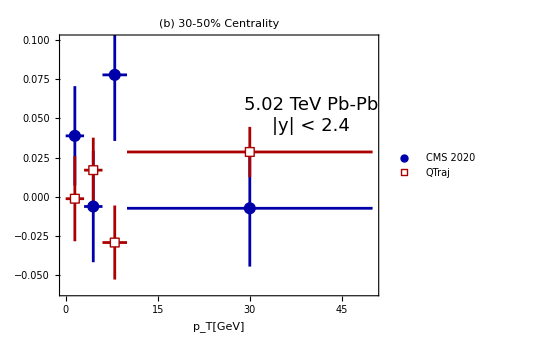
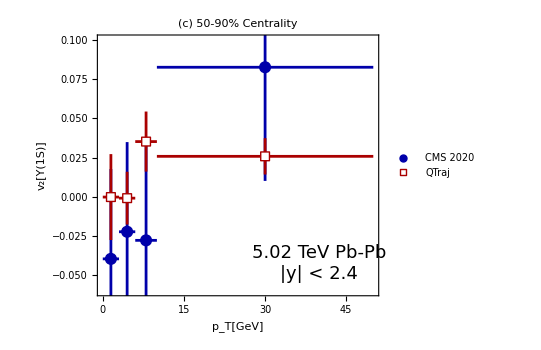
κ̂ = 4, γ̂ = 0, T_F = 190 MeV, τ_med = 0.6 fm, with jumps |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
CMSFig3plot=Grid[{{Text[Style["             "<>labelMap[dataDir],18]]},{panela,panelb,panelc}},Spacings->{0,0}]
```

```mathematica
Export[wd<>"/figures/cmsfig3-"<>figureNameMap[dataDir]<>".pdf",CMSFig3plot]
```

/home/sawin/Desktop/Bottomonia_AA/LHC/5 TeV/HNM/figures/cmsfig3-lhc-3d.pdf

#### Figure 4 from CMS Paper

```mathematica
ptbinCenters2={Around[1.5,1.5],Around[4.5,1.5],Around[10.5,4.5]}
```

{1.51.5,4.51.5,11.5.}

```mathematica
CMSfig4 = Partition[Riffle[ptbinCenters2,{
Around[0.012307,Sqrt[0.0194485^2+0.0165496^2]],
Around[-0.0124458,Sqrt[0.0197121^2+0.00980994^2]],
Around[0.0318967,Sqrt[0.018247^2+0.00575913^2]]}],2]
```

{{1.51.5,0.0120.026},{4.51.5,-0.0120.022},{11.5.,0.0320.019}}

```mathematica
CMSfig4alice = Partition[Riffle[ptbinCenters2,{Around[0.0139386095,0.05456941-0.0139386095],Around[-0.009578199,0.030494975+0.009578199],Around[0.0035327305,0.061417703-0.0035327305]}],2]
```

{{1.51.5,0.010.04},{4.51.5,0.000.04},{11.5.,0.000.06}}

```mathematica
res05601=computeVn[2,0,3,0.05,0.6];
res05602=computeVn[2,3,6,0.05,0.6];
res05603=computeVn[2,6,15,0.05,0.6];
allResults0560= {res05601,res05602,res05603}
```

{{-0.0050.016,-0.030.05,0.0150.031},{0.0250.015,0.040.05,0.0000.020},{-0.0040.011,-0.0150.024,0.0270.012}}

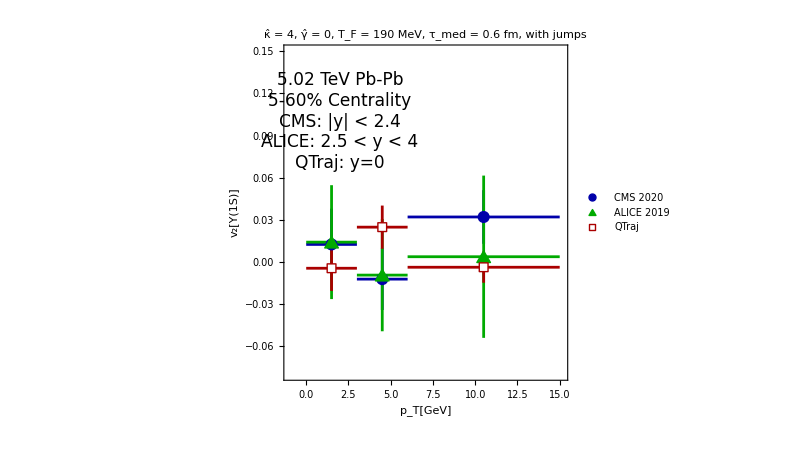

```mathematica
CMSFig4Plot=ListPlot[{CMSfig4,CMSfig4alice,Partition[Riffle[ptbinCenters2,allResults0560[[All,1]]],2]},IntervalMarkers->"Fences",IntervalMarkersStyle->{{AbsoluteThickness[2],Darker[Blue]},{AbsoluteThickness[2],Darker[Green]},{AbsoluteThickness[2],Darker[Red]}},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Blue]}],Darker[Blue],Disk[]},ImageSize->11],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Green]}],Darker[Green],Triangle[{{0,0},{2,3.4},{4,0}}]},ImageSize->14],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Red]}],White,Rectangle[]},ImageSize->9]},FrameLabel->{"p_T[GeV]","v_2[Υ(1S)]"},ImageSize->600,PlotLegends->Placed[LineLegend[{"CMS 2020","ALICE 2019","QTraj"},LabelStyle->18,LegendMarkerSize->12],{0.83,0.85}],PlotRange->{{-1,15.15},{-0.08,0.15}},Epilog->Inset[Style["5.02 TeV Pb-Pb\n5-60% Centrality\nCMS: |y| < 2.4\nALICE: 2.5 < y < 4\nQTraj: y=0",17,TextAlignment->Left],{2,0.10}],AspectRatio->3/4,Axes->True,PlotLabel->Style[labelMap[dataDir],18]]
```

```mathematica
Export[wd<>"/figures/cmsfig4-"<>figureNameMap[dataDir]<>".pdf",CMSFig4Plot]
```

/home/sawin/Desktop/Bottomonia_AA/LHC/5 TeV/HNM/figures/cmsfig4-lhc-3d.pdf

```mathematica
v21svpt2=Partition[Riffle[ptbinCenters2,allResults0560[[All,1]]],2];
fileName = wd<>"/figures/cmsfig4-"<>figureNameMap[dataDir]<>".m";
If[FileExistsQ[fileName],DeleteFile[fileName]];
Save[fileName,v21svpt2]
```

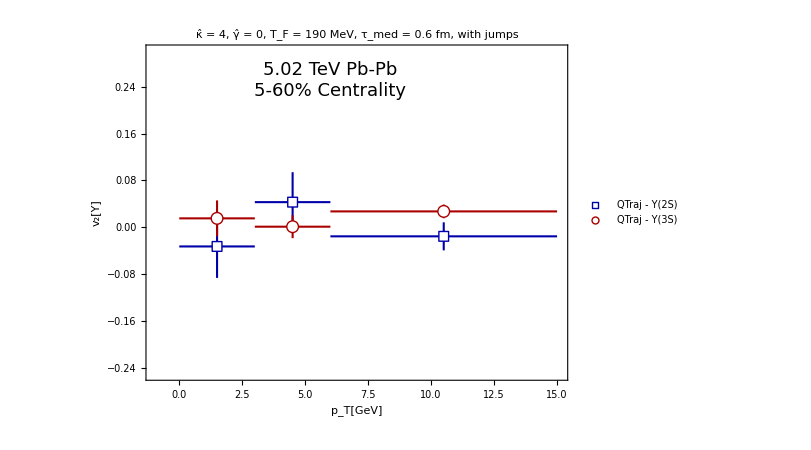

```mathematica
v2prediction=ListPlot[{Partition[Riffle[ptbinCenters2,allResults0560[[All,2]]],2],Partition[Riffle[ptbinCenters2,allResults0560[[All,3]]],2]},IntervalMarkers->"Fences",IntervalMarkersStyle->{{AbsoluteThickness[1.5],Darker[Blue]},{AbsoluteThickness[1.5],Darker[Red]}},PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Blue]}],White,Rectangle[]},ImageSize->10],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Red]}],White,Disk[]},ImageSize->12]},FrameLabel->{"p_T[GeV]","v_2[Υ]"},ImageSize->600,PlotLegends->Placed[LineLegend[{"QTraj - Υ(2S)","QTraj - Υ(3S)"},LabelStyle->18,LegendMarkerSize->12],{0.78,0.91}],Epilog->Inset[Style["5.02 TeV Pb-Pb\n5-60% Centrality",18,TextAlignment->Left],{6.0,0.25}],AspectRatio->3/4,Axes->True,PlotRange->{{-1,15.10},{-0.25,0.30}},PlotLabel->Style[labelMap[dataDir],18]]
```

```mathematica
Export[wd<>"/figures/v2prediction-"<>figureNameMap[dataDir]<>".pdf",v2prediction]
```

/home/sawin/Desktop/Bottomonia_AA/LHC/5 TeV/HNM/figures/v2prediction-lhc-3d.pdf

```mathematica
v22s3svpt={Partition[Riffle[ptbinCenters2,allResults0560[[All,2]]],2],Partition[Riffle[ptbinCenters2,allResults0560[[All,3]]],2]};
fileName = wd<>"/figures/v2prediction-"<>figureNameMap[dataDir]<>".m";
If[FileExistsQ[fileName],DeleteFile[fileName]];
Save[fileName,v22s3svpt]
```

```mathematica
?
```

### Integrated results for table

```mathematica
tableRes1=computeVn[2,2,15,0.05,0.6]
```

{0.0030.009,-0.0040.022,0.0180.010}

```mathematica
tableRes2=computeVn[2,0,30,0.1,0.9]
```

{0.0100.006,0.0110.011,0.0210.005}

### Result for v2 vs centrality in 20% bins

```mathematica
cPts = 5.;
dC  = 1/cPts;
cInts =Table[{(i-1)*dC,i*dC},{i,1,cPts }]
```

{{0.,0.2},{0.2,0.4},{0.4,0.6},{0.6,0.8},{0.8,1.}}

```mathematica
results  =ParallelTable[computeVn[2,0,40,cInts[[i,1]],cInts[[i,2]]],{i,1,cPts}]
```

{{0.0040.008,-0.0010.022,0.0110.011},{0.0060.011,0.0170.029,0.0310.013},{0.0250.012,0.0530.017,0.0450.009},{0.0180.009,0.0210.008,0.0180.005},{-0.0040.004,-0.0040.004,-0.0040.004}}

```mathematica
(*ListPlot3D[results,InterpolationOrder->3,IntervalMarkers->"Bands"]*)
```

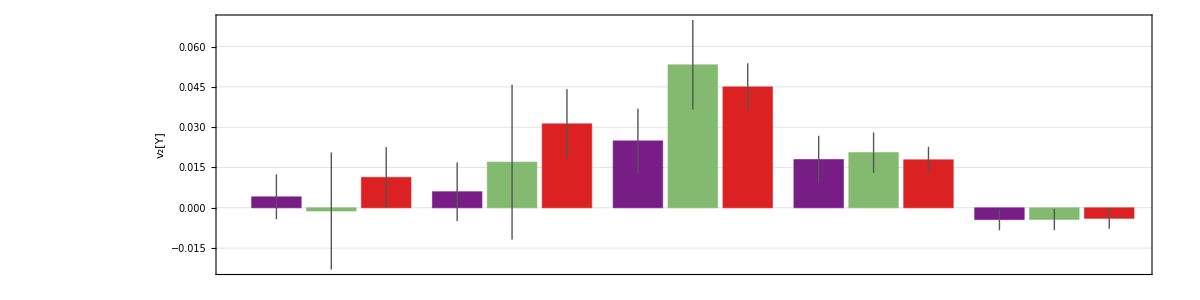

```mathematica
BarChart[results[[All,1;;3]],PlotTheme->"Detailed",AspectRatio->1/4,PlotRange->Automatic,(*ChartLabels->stateNames[[1;;5]],*)Frame->True,FrameStyle->AbsoluteThickness[1.5],ChartStyle->"Rainbow",FrameLabel->{"","v_2[Υ]"},IntervalMarkersStyle->{{Thick,Darker[Gray]}}, ImageSize->1200,BaseStyle->12]
```

```mathematica
y1sVsC=Join[{{0,Around[0,10^(-6)]}},Partition[Riffle[Mean/@cInts[[All]]*100,results[[All,1]]],2],{{100,Around[0,10^(-6)]}}]
y2sVsC=Join[{{0,Around[0,10^(-6)]}},Partition[Riffle[Mean/@cInts[[All]]*100,results[[All,2]]],2],{{100,Around[0,10^(-6)]}}]
(*y2pVsC=Join[{{0,Around[0,10^(-6)]}},Partition[Riffle[Mean/@cInts[[All]]*100,results[[All,3]]],2],{{100,Around[0,10^(-6)]}}]*)
y3sVsC=Join[{{0,Around[0,10^(-6)]}},Partition[Riffle[Mean/@cInts[[All]]*100,results[[All,3]]],2],{{100,Around[0,10^(-6)]}}]
(*y3pVsC=Join[{{0,Around[0,10^(-6)]}},Partition[Riffle[Mean/@cInts[[All]]*100,results[[All,5]]],2],{{100,Around[0,10^(-6)]}}]*)
```

{{0,0.01.010^-6},{10.,0.0040.008},{30.,0.0060.011},{50.,0.0250.012},{70.,0.0180.009},{90.,-0.0040.004},{100,0.01.010^-6}}

{{0,0.01.010^-6},{10.,-0.0010.022},{30.,0.0170.029},{50.,0.0530.017},{70.,0.0210.008},{90.,-0.0040.004},{100,0.01.010^-6}}

{{0,0.01.010^-6},{10.,0.0110.011},{30.,0.0310.013},{50.,0.0450.009},{70.,0.0180.005},{90.,-0.0040.004},{100,0.01.010^-6}}

```mathematica
myTicks=Range[0,cPts]100/cPts;
```

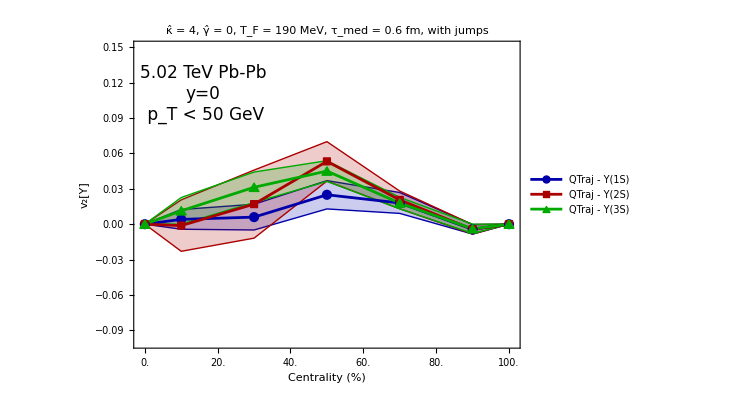

```mathematica
centralityPlotSwave=ListPlot[{y1sVsC,y2sVsC,y3sVsC},ImageSize->550,Joined->True,InterpolationOrder->1,PlotStyle->{{Darker[Blue],AbsoluteThickness[2]},{AbsoluteThickness[2],Darker[Red]},{AbsoluteThickness[2],Darker[Green]}},PlotRange->{{-1,101},{-0.10,0.15}},FrameLabel->{"Centrality (%)","v_2[Υ]"},IntervalMarkers->"Bands",PlotMarkers->{Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Blue]}],Darker[Blue],Disk[]},ImageSize->9],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Red]}],Darker[Red],Rectangle[]},ImageSize->7],Graphics[{EdgeForm[{AbsoluteThickness[1],Darker[Green]}],Darker[Green],Triangle[{{0,0},{1,1.7},{2,0}}]},ImageSize->10]},PlotLegends->Placed[LineLegend[{"QTraj - Υ(1S)","QTraj - Υ(2S)","QTraj - Υ(3S)"},LabelStyle->18],{0.8,0.82}],Epilog->Inset[Style["5.02 TeV Pb-Pb\ny=0\n p_T < 50 GeV",17,TextAlignment->Right],{16,0.11}],
FrameTicks->{{Automatic,Automatic},{myTicks,Automatic}},PlotLabel->Style[labelMap[dataDir],18]]
```